## 1

```mathematica
Clear["Global`*"];
dim=3/2;

SpinMatrices[s_]:=Module[{d,IzMat,superDiag,Iplus,Iminus,IxMat,IyMat},(*Define the dimension of the matrices:d=2s+1*)d=2 s+1;
(*Construct Iz:a diagonal matrix with entries m=s,s-1,...,-s*)IzMat=DiagonalMatrix[Table[m,{m,s,-s,-1}]];
(*Compute the superdiagonal elements for I+*)superDiag=Table[Sqrt[s (s+1)-(s-j) (s-j+1)],{j,1,d-1}];
(*Construct I+as a dense matrix with superdiagonal elements*)Iplus=Normal[SparseArray[Band[{1,2}]->superDiag,{d,d}]];
(*Construct I-as the transpose of I+*)Iminus=Transpose[Iplus];
(*Compute Ix and Iy from I+and I-*)IxMat=(Iplus+Iminus)/2;
IyMat=(Iplus-Iminus)/(2 I);
(*Return the three spin matrices*){IxMat,IyMat,IzMat}];

(*Assign the matrices*)
{Ix3half2,Iy3half2,Iz3half2}=SpinMatrices[dim];
Hmuti[ϕ1_,ϕ2_,ϕ3_]:=({{0, (√3)/2 ⅇ^(-ⅈ ϕ1), 0, 0}, {(√3)/2 ⅇ^(ⅈ ϕ1), 0, ⅇ^(-ⅈ ϕ2), 0}, {0, ⅇ^(ⅈ ϕ2), 0, (√3)/2 ⅇ^(-ⅈ ϕ3)}, {0, 0, (√3)/2 ⅇ^(ⅈ ϕ3), 0}});
Iplus5half2=Ix3half2+I*Iy3half2;
Iminus5half2=Ix3half2-I*Iy3half2;
UHmuti[ϕ1_,ϕ2_,ϕ3_,t_]:=MatrixExp[-I*Hmuti[ϕ1,ϕ2,ϕ3]*t] 
IniPhi={{1},{0},{0},{0}};

(*StateθϕInitial[θ_,ϕ_]:=MatrixExp[I*θ(Sin[ϕ]*Ix3half2-Cos[ϕ]*Iy3half2)].IniPhi*)

StateθϕInitial[θ_,ϕ_]:={{Cos[θ/2]^3},{1/4 √3 ⅇ^(ⅈ ϕ) Csc[θ/2] Sin[θ]^2},{1/2 √3 ⅇ^(2 ⅈ ϕ) Sin[θ/2] Sin[θ]},{ⅇ^(3 ⅈ ϕ) Sin[θ/2]^3}}

StateEvo[ϕ1_,ϕ2_,ϕ3_,t_,θ_,ϕ_]:=UHmuti[ϕ1,ϕ2,ϕ3,t].StateθϕInitial[θ,ϕ]
θ1[state1_]:=Module[{st=state1},
(*xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
*)
xVal=0;
zVal=0;
yVal=3/32 (9+7 Cos[2 t]+2 Sin[t]^2 (-3 Cos[2 ϕ11]+4 Sin[ϕ11]));
(*yVal={{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]))/(8 √2)},{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11)))},{-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))},{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}};*)


ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]
]
ϕ1[state1_]:=Module[{st=state1},
(*xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
*)
xVal=0;
zVal=0;
yVal=3/32 (9+7 Cos[2 t]+2 Sin[t]^2 (-3 Cos[2 ϕ11]+4 Sin[ϕ11]));
(*yVal={{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]))/(8 √2)},{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11)))},{-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))},{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}};*)
(*If[First[Flatten[yVal]]>0,First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]],2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]*)
ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]
]

In1[state_]:=-Ix3half2*Sin[ϕ1[state]]+Iy3half2*Cos[ϕ1[state]]
In2[state_]:=-Ix3half2*Cos[θ1[state]]Cos[ϕ1[state]]-Iy3half2*Cos[θ1[state]]Sin[ϕ1[state]]+Iz3half2*Sin[θ1[state]]
In1n2plusSqure[state_]:=ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state
In1n2minusSqure[state_]:=ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state
In1n2n2n1[state_]:=ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state
(*In1n2plusSqure[state_]:=ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state
In1n2minusSqure[state_]:=ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state
In1n2n2n1[state_]:=ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state
*)
ξSqure[state_]:= (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )
```

```mathematica
θ1[state1_]
```

π/2

```mathematica
ϕ1[state1_]
```

π/2

```mathematica
UHmuti[ϕ1,Pi/2,Pi-ϕ1,t].StateθϕInitial[θ,ϕ]//FullSimplify
```

{{1/16 ⅇ^(-1/2 ⅈ (3 t+2 ϕ1)) ((1+ⅇ^(ⅈ t)) Cos[θ/2]+ⅈ ⅇ^(ⅈ ϕ) (-1+ⅇ^(ⅈ t)) Sin[θ/2]) (ⅇ^(ⅈ (2 ϕ+ϕ1)) (-1+ⅇ^(ⅈ t))^2 (-1+Cos[θ])+ⅇ^(ⅈ ϕ1) (1+ⅇ^(ⅈ t))^2 (1+Cos[θ])-ⅈ ⅇ^(ⅈ ϕ) (-1+ⅇ^(2 ⅈ t)) (-3 ⅈ+ⅇ^(ⅈ ϕ1)) Sin[θ])},{1/8 √3 ⅇ^(-(3 ⅈ t)/2) (ⅈ ⅇ^(ⅈ (3 ϕ+ϕ1)) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t))+ⅇ^(ⅈ ϕ) (3+ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t)) Cot[θ/2]^2-ⅇ^(ⅈ ϕ1) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2 Cot[θ/2]^3+2 ⅇ^((3 ⅈ t)/2+2 ⅈ ϕ) Cot[θ/2] (Sin[t/2]-3 Sin[(3 t)/2])) Sin[θ/2]^3},{1/8 √3 ⅇ^(-(3 ⅈ t)/2) (ⅇ^(ⅈ (3 ϕ+ϕ1)) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2+ⅇ^(2 ⅈ ϕ) (3+ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t)) Cot[θ/2]+ⅈ ⅇ^(ⅈ ϕ1) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t)) Cot[θ/2]^3-2 ⅇ^((3 ⅈ t)/2+ⅈ ϕ) Cot[θ/2]^2 (Sin[t/2]-3 Sin[(3 t)/2])) Sin[θ/2]^3},{1/16 ⅇ^(-1/2 ⅈ (3 t+2 ϕ1)) ((-1+ⅇ^(ⅈ t)) Cos[θ/2]+ⅈ ⅇ^(ⅈ ϕ) (1+ⅇ^(ⅈ t)) Sin[θ/2]) (ⅈ ⅇ^(ⅈ (2 ϕ+ϕ1)) (1+ⅇ^(ⅈ t))^2 (-1+Cos[θ])+ⅈ ⅇ^(ⅈ ϕ1) (-1+ⅇ^(ⅈ t))^2 (1+Cos[θ])+ⅇ^(ⅈ ϕ) (-1+ⅇ^(2 ⅈ t)) (-3 ⅈ+ⅇ^(ⅈ ϕ1)) Sin[θ])}}

```mathematica
θ1[state1_]
```

1/2

```mathematica
ArcCos[0]
```

π/2

```mathematica
ϕ1[state1_]
```

1/2

```mathematica
Cosh[0]
```

1

```mathematica
Sinh[0]
```

0

```mathematica
In1[state_]//MatrixForm
```

```mathematica
({{0, -1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2], 0, 0}, {1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2], 0, -ⅈ Cos[1/2]-Sin[1/2], 0}, {0, ⅈ Cos[1/2]-Sin[1/2], 0, -1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]}, {0, 0, 1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2], 0}})
```

```mathematica
In1n2plusSqure[{{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]))/(8 √2)},{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11)))},{-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))},{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}}]//FullSimplify
```

```mathematica
{{3/16 ⅇ^(-ⅈ (t-t)) (Cos[t] (8 Cos[t]+2 ⅈ Sin[t] (1+3 Sin[ϕ11]))+Sin[t] (-2 ⅈ Cos[t] (1+3 Sin[ϕ11])+Sin[t] (-7 ⅈ Cos[ϕ11]+7 ⅈ Cos[ϕ11]+3 Cos[2 Re[ϕ11]]+11 Cosh[0]-2 (-2+Sin[ϕ11]+Sin[ϕ11])+7 Sinh[0])))}}//FullSimplify
```

{{3/16 (8 Cos[t]^2+Sin[t]^2 (15+3 Cos[2 Re[ϕ11]]-4 Sin[ϕ11]))}}

```mathematica
In1n2minusSqure[{{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]))/(8 √2)},{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11)))},{-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))},{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}}]//FullSimplify
```

```mathematica
{{3/32 ⅇ^(-ⅈ (t+ϕ11+ϕ11+Re[t])) (-8 Cos[t] Sin[t] (2 Cos[ϕ11]-ⅈ (-1+Sin[ϕ11]))+4 Sin[t] (-2 Cos[t] (2 Cos[ϕ11]+ⅈ (-1+Sin[ϕ11]))+Sin[t] (1+Sin[ϕ11]+ⅈ Cos[ϕ11] (1+3 Sin[ϕ11])+Sin[ϕ11]-ⅈ (Cos[ϕ11]+3 ⅇ^(-ⅈ ϕ11) Sin[ϕ11])))) (Cos[t+ϕ11+t+ϕ11]+ⅈ Sin[t+ϕ11+t+ϕ11])}}//FullSimplify
```

```mathematica
s
```

```mathematica
{{-3/8 ⅇ^(ⅈ (t-ϕ11-t)) Sin[t] (4 (1+ⅇ^(2 ⅈ ϕ11)) Cos[t]+ⅇ^(ⅈ ϕ11) Sin[t] (-1+Sin[ϕ11]) (1+3 Sin[ϕ11]))}}//FullSimplify
```

{{3/16 (-8 Cos[ϕ11] Sin[2 t]+Sin[t]^2 (-1+3 Cos[2 ϕ11]+4 Sin[ϕ11]))}}

```mathematica
In1n2n2n1[{{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]))/(8 √2)},{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11)))},{-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))},{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}}]//FullSimplify
```

```mathematica
{{3/8 ⅇ^(-ⅈ (t-t)) (2 Cos[t] Sin[t] (-1+2 ⅈ Cos[ϕ11]+Sin[ϕ11])+Sin[t] (2 Cos[t] (-1-2 ⅈ Cos[ϕ11]+Sin[ϕ11])-Sin[t] (Cos[ϕ11]+Cos[ϕ11]-2 ⅈ Sin[ϕ11]+2 ⅈ Sin[ϕ11]+3 Sin[2 ϕ11])))}}//FullSimplify
```

{{-3/4 Sin[t] (-2 Cos[t] (-1+Sin[ϕ11])+Cos[ϕ11] Sin[t] (1+3 Sin[ϕ11]))}}

```mathematica
ξSqure[{{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]))/(8 √2)},{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11)))},{-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))},{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}}]//FullSimplify
```

1/(8 √2)ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))) (1/4 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (3+ⅇ^(-2 ⅈ Conjugate[t])-2 Conjugate[Sin[t]] (Conjugate[Cos[t+ϕ11]]-ⅈ Conjugate[Sin[t+ϕ11]])) Sin[1/2] (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])+1/8 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (-3 ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11])-ⅇ^(-2 ⅈ Conjugate[t]) (ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11]))) ((-ⅈ Cos[1/2]-Sin[1/2]) (-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))+1/(8 √2)ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) (3-3 ⅇ^(-2 ⅈ Conjugate[t])+ⅈ ⅇ^(-ⅈ Conjugate[ϕ11]) (1+3 ⅇ^(-2 ⅈ Conjugate[t]))) (9/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))+1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11))) ((ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) Conjugate[ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]] Sin[1/2] (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))/(4 √2)+(ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) (3-3 ⅇ^(-2 ⅈ Conjugate[t])+ⅈ ⅇ^(-ⅈ Conjugate[ϕ11]) (1+3 ⅇ^(-2 ⅈ Conjugate[t]))) ((ⅈ Cos[1/2]-Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(8 √2)+1/8 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (-3 ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11])-ⅇ^(-2 ⅈ Conjugate[t]) (ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11]))) ((-ⅈ Cos[1/2]-Sin[1/2]) (ⅈ Cos[1/2]-Sin[1/2])+1/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])+(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))+1/(8 √2)ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (1/4 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (-3 ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11])-ⅇ^(-2 ⅈ Conjugate[t]) (ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11]))) Sin[1/2] (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])-1/8 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (3+ⅇ^(-2 ⅈ Conjugate[t])-2 Conjugate[Sin[t]] (Conjugate[Cos[t+ϕ11]]-ⅈ Conjugate[Sin[t+ϕ11]])) ((ⅈ Cos[1/2]-Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]))+(ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) Conjugate[ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]] (9/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(8 √2)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t])-√(((1/(8 √2)ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))) (1/4 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (3+ⅇ^(-2 ⅈ Conjugate[t])-2 Conjugate[Sin[t]] (Conjugate[Cos[t+ϕ11]]-ⅈ Conjugate[Sin[t+ϕ11]])) Sin[1/2] (-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+1/8 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (-3 ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11])-ⅇ^(-2 ⅈ Conjugate[t]) (ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11]))) ((-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])+(-ⅈ Cos[1/2]-Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))+1/(8 √2)ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) (3-3 ⅇ^(-2 ⅈ Conjugate[t])+ⅈ ⅇ^(-ⅈ Conjugate[ϕ11]) (1+3 ⅇ^(-2 ⅈ Conjugate[t]))) ((-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])+(1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))+1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11))) ((ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) Conjugate[ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]] Sin[1/2] (-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]))/(4 √2)+(ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) (3-3 ⅇ^(-2 ⅈ Conjugate[t])+ⅈ ⅇ^(-ⅈ Conjugate[ϕ11]) (1+3 ⅇ^(-2 ⅈ Conjugate[t]))) ((1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2])+(ⅈ Cos[1/2]-Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(8 √2)+1/8 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (-3 ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11])-ⅇ^(-2 ⅈ Conjugate[t]) (ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11]))) ((-ⅈ Cos[1/2]-Sin[1/2]) (-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2])+(ⅈ Cos[1/2]-Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])+(1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))+1/(8 √2)ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (1/4 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (-3 ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11])-ⅇ^(-2 ⅈ Conjugate[t]) (ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11]))) Sin[1/2] (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-1/8 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (3+ⅇ^(-2 ⅈ Conjugate[t])-2 Conjugate[Sin[t]] (Conjugate[Cos[t+ϕ11]]-ⅈ Conjugate[Sin[t+ϕ11]])) ((1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2])+(ⅈ Cos[1/2]-Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]))+(ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) Conjugate[ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]] ((-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])+(1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(8 √2)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t])-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (-(ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) (3-3 ⅇ^(-2 ⅈ Conjugate[t])+ⅈ ⅇ^(-ⅈ Conjugate[ϕ11]) (1+3 ⅇ^(-2 ⅈ Conjugate[t]))) Sin[1/2] (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]))/(4 √2)+(ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) Conjugate[ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]] ((-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])+(-ⅈ Cos[1/2]-Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(8 √2)-1/8 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (3+ⅇ^(-2 ⅈ Conjugate[t])-2 Conjugate[Sin[t]] (Conjugate[Cos[t+ϕ11]]-ⅈ Conjugate[Sin[t+ϕ11]])) ((-ⅈ Cos[1/2]-Sin[1/2]) (-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2])+(ⅈ Cos[1/2]-Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])+(1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))))^2+((1/(8 √2)ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))) (-1/4 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (3+ⅇ^(-2 ⅈ Conjugate[t])-2 Conjugate[Sin[t]] (Conjugate[Cos[t+ϕ11]]-ⅈ Conjugate[Sin[t+ϕ11]])) Sin[1/2] (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])+1/8 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (-3 ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11])-ⅇ^(-2 ⅈ Conjugate[t]) (ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11]))) ((-ⅈ Cos[1/2]-Sin[1/2]) (-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))+1/(8 √2)ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) (3-3 ⅇ^(-2 ⅈ Conjugate[t])+ⅈ ⅇ^(-ⅈ Conjugate[ϕ11]) (1+3 ⅇ^(-2 ⅈ Conjugate[t]))) (-9/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))+1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11))) (-(ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) Conjugate[ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]] Sin[1/2] (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))/(4 √2)+(ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) (3-3 ⅇ^(-2 ⅈ Conjugate[t])+ⅈ ⅇ^(-ⅈ Conjugate[ϕ11]) (1+3 ⅇ^(-2 ⅈ Conjugate[t]))) ((ⅈ Cos[1/2]-Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(8 √2)+1/8 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (-3 ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11])-ⅇ^(-2 ⅈ Conjugate[t]) (ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11]))) ((-ⅈ Cos[1/2]-Sin[1/2]) (ⅈ Cos[1/2]-Sin[1/2])-1/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])-(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))+1/(8 √2)ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (-1/4 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (-3 ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11])-ⅇ^(-2 ⅈ Conjugate[t]) (ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11]))) Sin[1/2] (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])-1/8 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (3+ⅇ^(-2 ⅈ Conjugate[t])-2 Conjugate[Sin[t]] (Conjugate[Cos[t+ϕ11]]-ⅈ Conjugate[Sin[t+ϕ11]])) ((ⅈ Cos[1/2]-Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]))+(ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) Conjugate[ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]] (-9/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(8 √2)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t])-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) ((ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) (3-3 ⅇ^(-2 ⅈ Conjugate[t])+ⅈ ⅇ^(-ⅈ Conjugate[ϕ11]) (1+3 ⅇ^(-2 ⅈ Conjugate[t]))) Sin[1/2] (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]))/(4 √2)+(ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) Conjugate[ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]] ((-ⅈ Cos[1/2]-Sin[1/2]) (-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(8 √2)-1/8 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (3+ⅇ^(-2 ⅈ Conjugate[t])-2 Conjugate[Sin[t]] (Conjugate[Cos[t+ϕ11]]-ⅈ Conjugate[Sin[t+ϕ11]])) ((-ⅈ Cos[1/2]-Sin[1/2]) (ⅈ Cos[1/2]-Sin[1/2])-1/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])-(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))))^2)-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (-(ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) (3-3 ⅇ^(-2 ⅈ Conjugate[t])+ⅈ ⅇ^(-ⅈ Conjugate[ϕ11]) (1+3 ⅇ^(-2 ⅈ Conjugate[t]))) Sin[1/2] (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]))/(4 √2)+(ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) Conjugate[ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]] ((-ⅈ Cos[1/2]-Sin[1/2]) (-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(8 √2)-1/8 √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (3+ⅇ^(-2 ⅈ Conjugate[t])-2 Conjugate[Sin[t]] (Conjugate[Cos[t+ϕ11]]-ⅈ Conjugate[Sin[t+ϕ11]])) ((-ⅈ Cos[1/2]-Sin[1/2]) (ⅈ Cos[1/2]-Sin[1/2])+1/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])+(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))

```mathematica
DensityPlot[ξSqure[{{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]))/(8 √2)},{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11)))},{-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))},{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}}],{t,0,3},{ϕ11,0,2Pi}]
```

-Graphics-

```mathematica
t=0;
ϕ11=0;
ξSqure[{{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]))/(8 √2)},{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11)))},{-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))},{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}}]
```

{{-1/(2 √2)ⅈ (√(3/2) Sin[1/2] (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])-1/2 ⅈ √(3/2) ((-ⅈ Cos[1/2]-Sin[1/2]) (-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))+(ⅈ (9/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(2 √2))+1/(2 √2)(-ⅈ √(3/2) Sin[1/2] (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])-1/2 √(3/2) ((ⅈ Cos[1/2]-Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]))+(9/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))/(2 √2))-1/2 √(3/2) (-(ⅈ Sin[1/2] (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]))/(√2)+((-ⅈ Cos[1/2]-Sin[1/2]) (-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))/(2 √2)-1/2 √(3/2) ((-ⅈ Cos[1/2]-Sin[1/2]) (ⅈ Cos[1/2]-Sin[1/2])+1/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])+(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))+1/2 ⅈ √(3/2) ((Sin[1/2] (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))/(√2)+(ⅈ ((ⅈ Cos[1/2]-Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(2 √2)-1/2 ⅈ √(3/2) ((-ⅈ Cos[1/2]-Sin[1/2]) (ⅈ Cos[1/2]-Sin[1/2])+1/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])+(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])+(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))-√((-1/(2 √2)ⅈ (√(3/2) Sin[1/2] (-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-1/2 ⅈ √(3/2) ((-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])+(-ⅈ Cos[1/2]-Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))+(ⅈ ((-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])+(1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(2 √2))+1/(2 √2)(-ⅈ √(3/2) Sin[1/2] (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-1/2 √(3/2) ((1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2])+(ⅈ Cos[1/2]-Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]))+((-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])+(1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))/(2 √2))-1/2 √(3/2) (-(ⅈ Sin[1/2] (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]))/(√2)+((-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])+(-ⅈ Cos[1/2]-Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))/(2 √2)-1/2 √(3/2) ((-ⅈ Cos[1/2]-Sin[1/2]) (-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2])+(ⅈ Cos[1/2]-Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])+(1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))+1/2 ⅈ √(3/2) ((Sin[1/2] (-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]))/(√2)+(ⅈ ((1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2])+(ⅈ Cos[1/2]-Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(2 √2)-1/2 ⅈ √(3/2) ((-ⅈ Cos[1/2]-Sin[1/2]) (-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2])+(ⅈ Cos[1/2]-Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])+(1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))))^2+(-1/(2 √2)ⅈ (-√(3/2) Sin[1/2] (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])-1/2 ⅈ √(3/2) ((-ⅈ Cos[1/2]-Sin[1/2]) (-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))+(ⅈ (-9/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(2 √2))+1/(2 √2)(ⅈ √(3/2) Sin[1/2] (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])-1/2 √(3/2) ((ⅈ Cos[1/2]-Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]))+(-9/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))/(2 √2))-1/2 √(3/2) ((ⅈ Sin[1/2] (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]))/(√2)+((-ⅈ Cos[1/2]-Sin[1/2]) (-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))/(2 √2)-1/2 √(3/2) ((-ⅈ Cos[1/2]-Sin[1/2]) (ⅈ Cos[1/2]-Sin[1/2])-1/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])-(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2])))+1/2 ⅈ √(3/2) (-(Sin[1/2] (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))/(√2)+(ⅈ ((ⅈ Cos[1/2]-Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2])))/(2 √2)-1/2 ⅈ √(3/2) ((-ⅈ Cos[1/2]-Sin[1/2]) (ⅈ Cos[1/2]-Sin[1/2])-1/4 Sin[1/2]^2+(-1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2]) (1/2 ⅈ √3 Cos[1/2]-1/2 √3 Sin[1/2])-(-Cos[1/2]^2-ⅈ Cos[1/2] Sin[1/2]) (-Cos[1/2]^2+ⅈ Cos[1/2] Sin[1/2])-(-1/2 √3 Cos[1/2]^2-1/2 ⅈ √3 Cos[1/2] Sin[1/2]) (-1/2 √3 Cos[1/2]^2+1/2 ⅈ √3 Cos[1/2] Sin[1/2]))))^2)}}

```mathematica
StateEvo[ϕ11,Pi/2,Pi-ϕ11,t,Pi/2,Pi/2]//FullSimplify
```

```mathematica
ST1={{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]))/(8 √2)},{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11)))},{-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))},{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}};
CJST1={{(ⅇ^(1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(-ⅈ ϕ11) (1+3 ⅇ^(-2 ⅈ t))+6 ⅇ^(-ⅈ t) Sin[t]))/(8 √2),1/8 √(3/2) ⅇ^(3/2 ⅈ t) (-3 ⅈ+ⅇ^(-ⅈ ϕ11)-ⅇ^(-2 ⅈ t) (ⅈ+ⅇ^(-ⅈ ϕ11))),-1/8 √(3/2) ⅇ^(3/2 ⅈ t) (3+ⅇ^(-2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]-ⅈ Sin[t+ϕ11])),(ⅇ^(1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(-2 ⅈ t)+ⅈ ⅇ^(-ⅈ ϕ11) (1+3 ⅇ^(-2 ⅈ t))))/(8 √2)}};
```

```mathematica
CJST1.Iy3half2.ST1//FullSimplify
```

{{3/32 (9+7 Cos[2 t]+2 Sin[t]^2 (-3 Cos[2 ϕ11]+4 Sin[ϕ11]))}}

```mathematica
ConjugateTranspose[ST1]
```

```mathematica
{{(ⅇ^(1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(-ⅈ ϕ11) (1+3 ⅇ^(-2 ⅈ t))+6 ⅇ^(-ⅈ t) Sin[t]))/(8 √2),1/8 √(3/2) ⅇ^(3/2 ⅈ t) (-3 ⅈ+ⅇ^(-ⅈ ϕ11)-ⅇ^(-2 ⅈ t) (ⅈ+ⅇ^(-ⅈ ϕ11))),-1/8 √(3/2) ⅇ^(3/2 ⅈ t) (3+ⅇ^(-2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]-ⅈ Sin[t+ϕ11])),(ⅇ^(1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(-2 ⅈ t)+ⅈ ⅇ^(-ⅈ ϕ11) (1+3 ⅇ^(-2 ⅈ t))))/(8 √2)}}
```

```mathematica
ConjugateTranspose[ST1].Iy3half2.ST1//FullSimplify
```

{{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11))) (-1/16 ⅈ √(3/2) ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) Conjugate[ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]]-1/8 ⅈ √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (3+ⅇ^(-2 ⅈ Conjugate[t])-2 Conjugate[Sin[t]] (Conjugate[Cos[t+ϕ11]]-ⅈ Conjugate[Sin[t+ϕ11]])))+3/256 ⅈ ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)+3/2 ⅈ Conjugate[t]) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))) (3+ⅇ^(-2 ⅈ Conjugate[t])-2 Conjugate[Sin[t]] (Conjugate[Cos[t+ϕ11]]-ⅈ Conjugate[Sin[t+ϕ11]]))+3/256 ⅈ ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)+3/2 ⅈ Conjugate[t]) (-3 ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11])-ⅇ^(-2 ⅈ Conjugate[t]) (ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11]))) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t])-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (1/16 ⅈ √(3/2) ⅇ^(1/2 ⅈ (3 Conjugate[t]+2 Conjugate[ϕ11])) (3-3 ⅇ^(-2 ⅈ Conjugate[t])+ⅈ ⅇ^(-ⅈ Conjugate[ϕ11]) (1+3 ⅇ^(-2 ⅈ Conjugate[t])))-1/8 ⅈ √(3/2) ⅇ^(3/2 ⅈ Conjugate[t]) (-3 ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11])-ⅇ^(-2 ⅈ Conjugate[t]) (ⅈ+ⅇ^(-ⅈ Conjugate[ϕ11])))) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))}}

```mathematica
{{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11))) (-1/16 ⅈ √(3/2) ⅇ^(1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(-ⅈ ϕ11) (1+3 ⅇ^(-2 ⅈ t))+6 ⅇ^(-ⅈ t) Sin[t])-1/8 ⅈ √(3/2) ⅇ^(3/2 ⅈ t) (3+ⅇ^(-2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]-ⅈ Sin[t+ϕ11])))+3/256 ⅈ ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)+3/2 ⅈ t) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))) (3+ⅇ^(-2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]-ⅈ Sin[t+ϕ11]))+3/256 ⅈ ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)+3/2 ⅈ t) (-3 ⅈ+ⅇ^(-ⅈ ϕ11)-ⅇ^(-2 ⅈ t) (ⅈ+ⅇ^(-ⅈ ϕ11))) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t])-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (1/16 ⅈ √(3/2) ⅇ^(1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(-2 ⅈ t)+ⅈ ⅇ^(-ⅈ ϕ11) (1+3 ⅇ^(-2 ⅈ t)))-1/8 ⅈ √(3/2) ⅇ^(3/2 ⅈ t) (-3 ⅈ+ⅇ^(-ⅈ ϕ11)-ⅇ^(-2 ⅈ t) (ⅈ+ⅇ^(-ⅈ ϕ11)))) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))}}//FullSimplify
```

```mathematica
ξSqure[{{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]))/(8 √2)},{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11)))},{-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))},{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}}]
```

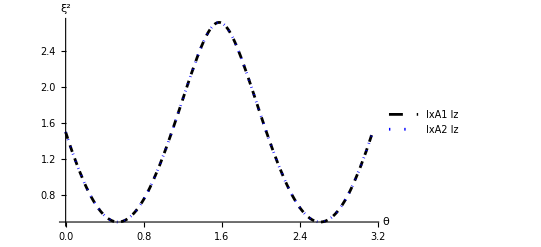

```mathematica
Plot[{ξSqure[StateEvo[-3.2010852203572133-Pi,-1.5707963031116705+Pi,+0.05949256001795611-Pi,t,Pi/2,Pi/2]],ξSqure[StateEvo[+0.05949256001795611,-1.5707963031116705,-3.2010852203572133,t,Pi/2,Pi/2]]},{t,0,Pi/1},PlotStyle->{{Black,Dashed},{Blue,Dotted},Red},AxesLabel->{"θ","ξ^2"},AxesStyle->Directive[Thick,Black],PlotLegends->{"IxA1 Iz","IxA2 Iz","IxA3 Iz"}]
```

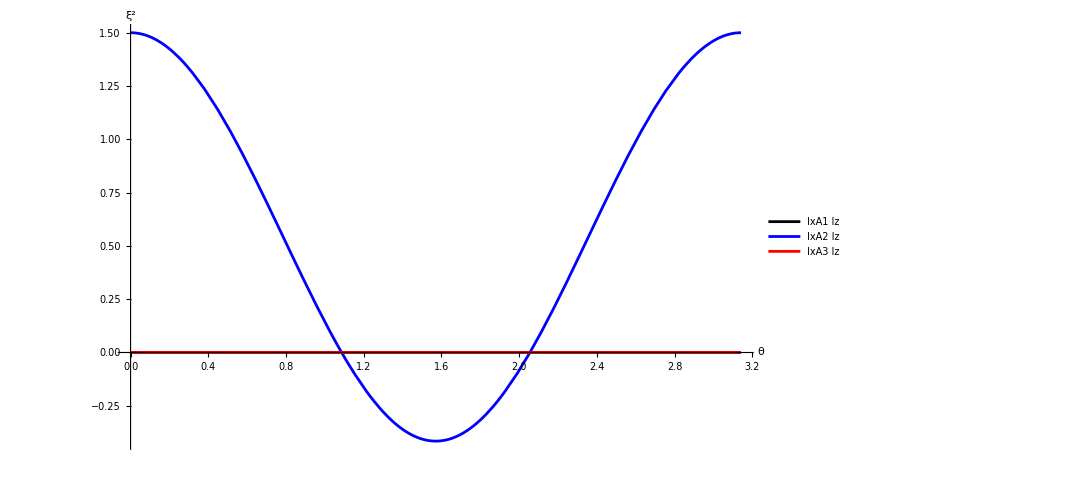

```mathematica
Plot[{Chop[ConjugateTranspose[StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2]].Ix3half2.StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2]],ConjugateTranspose[StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2]].Iy3half2.StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2],Chop[ConjugateTranspose[StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2]].Iz3half2.StateEvo[3.2010852203572133,1.5707963031116705,-0.05949256001795611,t,Pi/2,Pi/2]]},{t,0,Pi/1},PlotStyle->{Black,Blue,Red},AxesLabel->{"θ","ξ^2"},AxesStyle->Directive[Thick,Black],PlotLegends->{"IxA1 Iz","IxA2 Iz","IxA3 Iz"}]
```

```mathematica
ALLIZ=ListPlot[{IxA1Iz,IxA2Iz,IxA3Iz,IxA4Iz,IyA1Iz,IyA2Iz,IyA3Iz,IyA4Iz},Joined->True,PlotStyle->{Black,Blue,Red,Green,{Black,Dashed},{Blue,Dashed},{Red,Dashed},{Green,Dashed}},Joined->False,AxesLabel->{"θ","ξ^2"},AxesStyle->Directive[Thick,Black],PlotLegends->{"IxA1 Iz","IxA2 Iz","IxA3 Iz","IxA4 Iz","IyA1 Iz","IyA2 Iz","IyA3 Iz","IyA4 Iz"},PlotRange->{{0,200},{0.2,1.1}}]
```

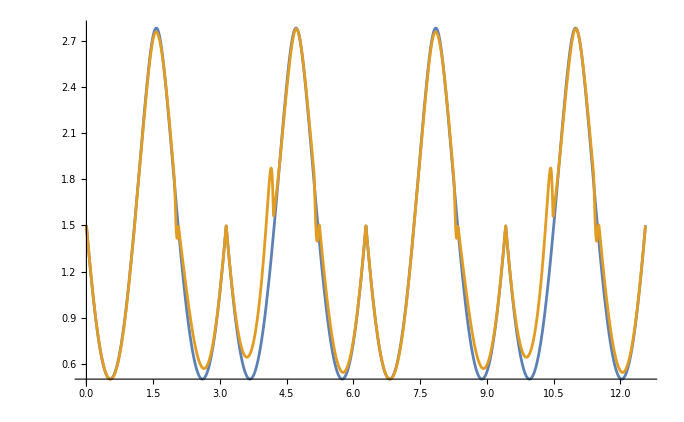

```mathematica
Plot[{ξSqure[StateEvo[3.2223358198961938,1.5707963292390268,-0.08074321213514413,t,Pi/2,Pi/2]],ξSqure[StateEvo[2.456380154124866,-1.2983350545682835,0.5625102484898132,t,Pi/2,Pi/2]]},{t,0,4Pi}]
```

```mathematica
StateEvo[ϕ11,ϕ2,ϕ3,t,Pi/4,Pi/4]//FullSimplify
```

```mathematica
stpihalf4={{1/64 ⅇ^(-1/2 ⅈ (3 t+2 (ϕ11+ϕ2+ϕ3))) (-8 (-1)^(3/4) (-1+ⅇ^(ⅈ t))^3-8 ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (1+ⅇ^(ⅈ t))^3 Cot[π/8]+6 ⅈ √2 ⅇ^(ⅈ ϕ3) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t)) Csc[π/8]^2-3 (-1)^(1/4) ⅇ^(ⅈ (ϕ2+ϕ3)) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2 Csc[π/8]^4+2 √2 ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (1+ⅇ^(ⅈ t))^3 Csc[π/8]^4) Sin[π/8]^3},{1/64 √3 ⅇ^(-1/2 ⅈ (3 t+2 (ϕ2+ϕ3))) ((1-ⅈ) √(1+1/(√2)) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t))-√(2-√2) ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2-3 √(2+√2) ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2+(1+ⅈ) √(2+√2) ⅇ^(ⅈ (ϕ2+ϕ3)) (3+ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t))+√(1-1/(√2)) (-1+ⅇ^(ⅈ t)) ((3-3 ⅈ)-(3-3 ⅈ) Cos[2 t]-(3+3 ⅈ) Sin[2 t]+4 (1+3 Cos[t]) (-ⅈ Cos[t+ϕ3]+Sin[t+ϕ3])))},{1/64 √3 ⅇ^(-1/2 ⅈ (3 t+2 ϕ3)) (√(2-√2) ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t))+3 √(2+√2) ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t))+(-1)^(3/4) √(2+√2) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2+(1+ⅈ) √(2+√2) ⅇ^(ⅈ (ϕ2+ϕ3)) (3-ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)-3 ⅇ^(3 ⅈ t))+√(1-1/(√2)) (1+ⅇ^(ⅈ t)) ((-3+3 ⅈ)+(3-3 ⅈ) Cos[2 t]+(3+3 ⅈ) Sin[2 t]+(-1+3 Cos[t]) (4 ⅈ Cos[t+ϕ3]-4 Sin[t+ϕ3])))},{1/8 ⅇ^(-(3 ⅈ t)/2) ((1+√2) ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(ⅈ t))^3+(4 (1+√2) ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(ⅈ t))^3)/(-2+√2)+6 (-1)^(1/4) (3/2+√2) ⅇ^(ⅈ (ϕ2+ϕ3)) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t))+(-1)^(3/4) (1+ⅇ^(ⅈ t))^3+ⅇ^(ⅈ ϕ3) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2 Root"-7.24" ⅈRoot[81+54 #1^2+#1^4&,3]0.) Sin[π/8]^3}};
```

```mathematica
Expand[Root"-7.24" ⅈRoot[81+54 #1^2+#1^4&,3]0.]
```

Root-7.24 ⅈRoot[81+54 #1^2+#1^4&,3]0.

```mathematica
ConjugateTranspose[stpihalf4]//FullSimplify
```

```mathematica
{{1/64 ⅇ^(1/2 ⅈ (3 t+2 (ϕ11+ϕ2+ϕ3))) Conjugate[-8 (-1)^(3/4) (-1+ⅇ^((-ⅈ )t))^3-8 ⅇ^((-ⅈ )(ϕ11+ϕ2+ϕ3)) (1+ⅇ^((-ⅈ )t))^3 Cot[π/8]+6 (-ⅈ )√2 ⅇ^((-ⅈ )ϕ3) (-1+ⅇ^((-ⅈ )t))^2 (1+ⅇ^((-ⅈ )t)) Csc[π/8]^2-3 (-1)^(1/4) ⅇ^((-ⅈ )(ϕ2+ϕ3)) (-1+ⅇ^((-ⅈ )t)) (1+ⅇ^((-ⅈ )t))^2 Csc[π/8]^4+2 √2 ⅇ^((-ⅈ )(ϕ11+ϕ2+ϕ3)) (1+ⅇ^((-ⅈ )t))^3 Csc[π/8]^4] Sin[π/8]^3,1/64 √3 ⅇ^(1/2 ⅈ (3 t+2 (ϕ2+ϕ3))) Conjugate[(1-(-ⅈ )) √(1+1/(√2)) (-1+ⅇ^((-ⅈ ) t))^2 (1+ⅇ^((-ⅈ ) t))-√(2-√2) ⅇ^((-ⅈ ) (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^((-ⅈ ) t)) (1+ⅇ^((-ⅈ ) t))^2-3 √(2+√2) ⅇ^((-ⅈ ) (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^((-ⅈ ) t)) (1+ⅇ^((-ⅈ ) t))^2+(1+(-ⅈ )) √(2+√2) ⅇ^((-ⅈ ) (ϕ2+ϕ3)) (3+ⅇ^((-ⅈ ) t)+ⅇ^(2 (-ⅈ ) t)+3 ⅇ^(3 (-ⅈ ) t))+√(1-1/(√2)) (-1+ⅇ^((-ⅈ ) t)) ((3-3 (-ⅈ ))-(3-3 (-ⅈ )) Cos[2 t]-(3+3 (-ⅈ )) Sin[2 t]+4 (1+3 Cos[t]) (-(-ⅈ ) Cos[t+ϕ3]+Sin[t+ϕ3]))],1/64 √3 ⅇ^(1/2 ⅈ (3 t+2 ϕ3)) Conjugate[√(2-√2) ⅇ^((-ⅈ ) (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^((-ⅈ ) t))^2 (1+ⅇ^((-ⅈ ) t))+3 √(2+√2) ⅇ^((-ⅈ ) (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^((-ⅈ ) t))^2 (1+ⅇ^((-ⅈ ) t))+(-1)^(3/4) √(2+√2) (-1+ⅇ^((-ⅈ ) t)) (1+ⅇ^((-ⅈ ) t))^2+(1+(-ⅈ )) √(2+√2) ⅇ^((-ⅈ ) (ϕ2+ϕ3)) (3-ⅇ^((-ⅈ ) t)+ⅇ^(2 (-ⅈ ) t)-3 ⅇ^(3 (-ⅈ ) t))+√(1-1/(√2)) (1+ⅇ^((-ⅈ ) t)) ((-3+3 (-ⅈ ))+(3-3 (-ⅈ )) Cos[2 t]+(3+3 (-ⅈ )) Sin[2 t]+(-1+3 Cos[t]) (4 (-ⅈ ) Cos[t+ϕ3]-4 Sin[t+ϕ3]))],1/8 ⅇ^(3/2 ⅈ t) Conjugate[(1+√2) ⅇ^((-ⅈ ) (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^((-ⅈ ) t))^3+(4 (1+√2) ⅇ^((-ⅈ ) (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^((-ⅈ ) t))^3)/(-2+√2)+6 (-1)^(1/4) (3/2+√2) ⅇ^((-ⅈ ) (ϕ2+ϕ3)) (-1+ⅇ^((-ⅈ ) t))^2 (1+ⅇ^((-ⅈ ) t))+(-1)^(3/4) (1+ⅇ^((-ⅈ ) t))^3+ⅇ^((-ⅈ ) ϕ3) (-1+ⅇ^((-ⅈ ) t)) (1+ⅇ^((-ⅈ ) t))^2 Root"-7.24" ⅈRoot[81+54 #1^2+#1^4&,3]0.] Sin[π/8]^3}}
```

```mathematica
ConjugateTranspose[StateEvo[ϕ11,ϕ2,ϕ3,t,Pi/4,Pi/4]].Ix3half2.StateEvo[ϕ11,ϕ2,ϕ3,t,Pi/4,Pi/4]
```

```mathematica
{{1/2 √3 ((-3/8 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)+3/8 ⅇ^((ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)+1/8 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)-1/8 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)) Cos[π/8]^3+1/8 √3 ⅇ^((ⅈ π)/4) (-1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)+1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)) Csc[π/8]+1/2 ⅈ √(3/2) (1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ3)-1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ3)) Sin[π/8]+ⅇ^((3 ⅈ π)/4) (3/8 ⅇ^(-(ⅈ t)/2)+3/8 ⅇ^((ⅈ t)/2)+1/8 ⅇ^(-(3 ⅈ t)/2)+1/8 ⅇ^((3 ⅈ t)/2)) Sin[π/8]^3) ((-1/8 √3 ⅇ^(-((-ⅈ) t)/2+(-ⅈ) ϕ11+(-ⅈ) ϕ2)-1/8 √3 ⅇ^(((-ⅈ) t)/2+(-ⅈ) ϕ11+(-ⅈ) ϕ2)+1/8 √3 ⅇ^(-(3 (-ⅈ) t)/2+(-ⅈ) ϕ11+(-ⅈ) ϕ2)+1/8 √3 ⅇ^((3 (-ⅈ) t)/2+(-ⅈ) ϕ11+(-ⅈ) ϕ2)) Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) (-1/8 ⅇ^(-((-ⅈ) t)/2+(-ⅈ) ϕ2)+1/8 ⅇ^(((-ⅈ) t)/2+(-ⅈ) ϕ2)+3/8 ⅇ^(-(3 (-ⅈ) t)/2+(-ⅈ) ϕ2)-3/8 ⅇ^((3 (-ⅈ) t)/2+(-ⅈ) ϕ2)) Csc[π/8]-1/2 ⅈ √(3/2) (1/8 ⅇ^(-1/2 ⅈ t)+1/8 ⅇ^(1/2 ⅈ t)+3/8 ⅇ^(-3/2 ⅈ t)+3/8 ⅇ^(3/2 ⅈ t)) Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) (1/8 √3 ⅇ^(-((-ⅈ) t)/2-(-ⅈ) ϕ3)-1/8 √3 ⅇ^(((-ⅈ) t)/2-(-ⅈ) ϕ3)+1/8 √3 ⅇ^(-(3 (-ⅈ) t)/2-(-ⅈ) ϕ3)-1/8 √3 ⅇ^((3 (-ⅈ) t)/2-(-ⅈ) ϕ3)) Sin[π/8]^3)+1/2 √3 ((3/8 ⅇ^(-(ⅈ t)/2)+3/8 ⅇ^((ⅈ t)/2)+1/8 ⅇ^(-(3 ⅈ t)/2)+1/8 ⅇ^((3 ⅈ t)/2)) Cos[π/8]^3+1/8 √3 ⅇ^((ⅈ π)/4) (1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ11)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11)-1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11)) Csc[π/8]+1/2 ⅈ √(3/2) (-1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)+1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)) Sin[π/8]+ⅇ^((3 ⅈ π)/4) (-3/8 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)+3/8 ⅇ^((ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)+1/8 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)-1/8 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)) Sin[π/8]^3) ((1/8 √3 ⅇ^(-((-ⅈ) t)/2+(-ⅈ) ϕ11)-1/8 √3 ⅇ^(((-ⅈ) t)/2+(-ⅈ) ϕ11)+1/8 √3 ⅇ^(-(3 (-ⅈ) t)/2+(-ⅈ) ϕ11)-1/8 √3 ⅇ^((3 (-ⅈ) t)/2+(-ⅈ) ϕ11)) Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) (1/8 ⅇ^(-1/2 ⅈ t)+1/8 ⅇ^(1/2 ⅈ t)+3/8 ⅇ^(-3/2 ⅈ t)+3/8 ⅇ^(3/2 ⅈ t)) Csc[π/8]-1/2 ⅈ √(3/2) Conjugate[-1/8 ⅇ^(-((-ⅈ) t)/2-(-ⅈ) ϕ2)+1/8 ⅇ^(((-ⅈ) t)/2-(-ⅈ) ϕ2)+3/8 ⅇ^(-(3 (-ⅈ) t)/2-(-ⅈ) ϕ2)-3/8 ⅇ^((3 (-ⅈ) t)/2-(-ⅈ) ϕ2)] Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) (-1/8 √3 ⅇ^(-((-ⅈ)t)/2-(-ⅈ)ϕ2-(-ⅈ)ϕ3)-1/8 √3 ⅇ^(((-ⅈ)t)/2-(-ⅈ)ϕ2-(-ⅈ)ϕ3)+1/8 √3 ⅇ^(-(3 (-ⅈ)t)/2-(-ⅈ)ϕ2-(-ⅈ)ϕ3)+1/8 √3 ⅇ^((3 (-ⅈ)t)/2-(-ⅈ)ϕ2-(-ⅈ)ϕ3)) Sin[π/8]^3)+((-1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)+1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)) Cos[π/8]^3+1/8 √3 ⅇ^((ⅈ π)/4) (-1/8 ⅇ^(-(ⅈ t)/2+ⅈ ϕ2)+1/8 ⅇ^((ⅈ t)/2+ⅈ ϕ2)+3/8 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ2)-3/8 ⅇ^((3 ⅈ t)/2+ⅈ ϕ2)) Csc[π/8]+1/2 ⅈ √(3/2) (1/8 ⅇ^(-(ⅈ t)/2)+1/8 ⅇ^((ⅈ t)/2)+3/8 ⅇ^(-(3 ⅈ t)/2)+3/8 ⅇ^((3 ⅈ t)/2)) Sin[π/8]+ⅇ^((3 ⅈ π)/4) (1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ3)-1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ3)) Sin[π/8]^3) ((1/8 √3 ⅇ^(-((-ⅈ) t)/2+(-ⅈ) ϕ11)-1/8 √3 ⅇ^(((-ⅈ) t)/2+(-ⅈ) ϕ11)+1/8 √3 ⅇ^(-(3 (-ⅈ) t)/2+(-ⅈ) ϕ11)-1/8 √3 ⅇ^((3 (-ⅈ) t)/2+(-ⅈ) ϕ11)) Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) (1/8 ⅇ^(-1/2 ⅈ t)+1/8 ⅇ^(1/2 ⅈ t)+3/8 ⅇ^(-3/2 ⅈ t)+3/8 ⅇ^(3/2 ⅈ t)) Csc[π/8]-1/2 ⅈ √(3/2) (-1/8 ⅇ^(-((-ⅈ) t)/2-(-ⅈ) ϕ2)+1/8 ⅇ^(((-ⅈ) t)/2-(-ⅈ) ϕ2)+3/8 ⅇ^(-(3 (-ⅈ) t)/2-(-ⅈ) ϕ2)-3/8 ⅇ^((3 (-ⅈ) t)/2-(-ⅈ) ϕ2)) Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) (-1/8 √3 ⅇ^(-((-ⅈ)t)/2-(-ⅈ)ϕ2-(-ⅈ)ϕ3)-1/8 √3 ⅇ^(((-ⅈ)t)/2-(-ⅈ)ϕ2-(-ⅈ)ϕ3)+1/8 √3 ⅇ^(-(3 (-ⅈ)t)/2-(-ⅈ)ϕ2-(-ⅈ)ϕ3)+1/8 √3 ⅇ^((3 (-ⅈ)t)/2-(-ⅈ)ϕ2-(-ⅈ)ϕ3)) Sin[π/8]^3+1/2 √3 ((-3/8 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)+3/8 ⅇ^((ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)+1/8 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)-1/8 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)) Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) (-1/8 √3 ⅇ^(-((-ⅈ) t)/2+(-ⅈ) ϕ2+(-ⅈ) ϕ3)-1/8 √3 ⅇ^(((-ⅈ) t)/2+(-ⅈ) ϕ2+(-ⅈ) ϕ3)+1/8 √3 ⅇ^(-(3 (-ⅈ) t)/2+(-ⅈ) ϕ2+(-ⅈ) ϕ3)+1/8 √3 ⅇ^((3 (-ⅈ) t)/2+(-ⅈ) ϕ2+(-ⅈ) ϕ3)) Csc[π/8]-1/2 ⅈ √(3/2) (1/8 √3 ⅇ^(-((-ⅈ) t)/2+(-ⅈ) ϕ3)-1/8 √3 ⅇ^(((-ⅈ) t)/2+(-ⅈ) ϕ3)+1/8 √3 ⅇ^(-(3 (-ⅈ) t)/2+(-ⅈ) ϕ3)-1/8 √3 ⅇ^((3 (-ⅈ) t)/2+(-ⅈ) ϕ3)) Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) (3/8 ⅇ^(-1/2 ⅈ t)+3/8 ⅇ^(1/2 ⅈ t)+1/8 ⅇ^(-3/2 ⅈ t)+1/8 ⅇ^(3/2 ⅈ t)) Sin[π/8]^3))+((1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ11)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11)-1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11)) Cos[π/8]^3+1/8 √3 ⅇ^((ⅈ π)/4) (1/8 ⅇ^(-(ⅈ t)/2)+1/8 ⅇ^((ⅈ t)/2)+3/8 ⅇ^(-(3 ⅈ t)/2)+3/8 ⅇ^((3 ⅈ t)/2)) Csc[π/8]+1/2 ⅈ √(3/2) (-1/8 ⅇ^(-(ⅈ t)/2-ⅈ ϕ2)+1/8 ⅇ^((ⅈ t)/2-ⅈ ϕ2)+3/8 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ2)-3/8 ⅇ^((3 ⅈ t)/2-ⅈ ϕ2)) Sin[π/8]+ⅇ^((3 ⅈ π)/4) (-1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)+1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)) Sin[π/8]^3) ((-1/8 √3 ⅇ^(-((-ⅈ) t)/2+(-ⅈ) ϕ11+(-ⅈ) ϕ2)-1/8 √3 ⅇ^(((-ⅈ) t)/2+(-ⅈ) ϕ11+(-ⅈ) ϕ2)+1/8 √3 ⅇ^(-(3 (-ⅈ) t)/2+(-ⅈ) ϕ11+(-ⅈ) ϕ2)+1/8 √3 ⅇ^((3 (-ⅈ) t)/2+(-ⅈ) ϕ11+(-ⅈ) ϕ2)) Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) Conjugate[-1/8 ⅇ^(-((-ⅈ) t)/2+(-ⅈ) ϕ2)+1/8 ⅇ^(((-ⅈ) t)/2+(-ⅈ) ϕ2)+3/8 ⅇ^(-(3 (-ⅈ) t)/2+(-ⅈ) ϕ2)-3/8 ⅇ^((3 (-ⅈ) t)/2+(-ⅈ) ϕ2)] Csc[π/8]-1/2 ⅈ √(3/2) (1/8 ⅇ^(-1/2 ⅈ t)+1/8 ⅇ^(1/2 ⅈ t)+3/8 ⅇ^(-3/2 ⅈ t)+3/8 ⅇ^(3/2 ⅈ t)) Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) (1/8 √3 ⅇ^(-((-ⅈ) t)/2-(-ⅈ) ϕ3)-1/8 √3 ⅇ^(((-ⅈ) t)/2-(-ⅈ) ϕ3)+1/8 √3 ⅇ^(-(3 (-ⅈ) t)/2-(-ⅈ) ϕ3)-1/8 √3 ⅇ^((3 (-ⅈ) t)/2-(-ⅈ) ϕ3)) Sin[π/8]^3+1/2 √3 ((3/8 ⅇ^(-1/2 ⅈ t)+3/8 ⅇ^(1/2 ⅈ t)+1/8 ⅇ^(-3/2 ⅈ t)+1/8 ⅇ^(3/2 ⅈ t)) Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) (1/8 √3 ⅇ^(-((-ⅈ) t)/2-(-ⅈ) ϕ11)-1/8 √3 ⅇ^(((-ⅈ) t)/2-(-ⅈ) ϕ11)+1/8 √3 ⅇ^(-(3 (-ⅈ) t)/2-(-ⅈ) ϕ11)-1/8 √3 ⅇ^((3 (-ⅈ) t)/2-(-ⅈ) ϕ11)) Csc[π/8]-1/2 ⅈ √(3/2) (-1/8 √3 ⅇ^(-((-ⅈ) t)/2-(-ⅈ) ϕ11-(-ⅈ) ϕ2)-1/8 √3 ⅇ^(((-ⅈ) t)/2-(-ⅈ) ϕ11-(-ⅈ) ϕ2)+1/8 √3 ⅇ^(-(3 (-ⅈ) t)/2-(-ⅈ) ϕ11-(-ⅈ) ϕ2)+1/8 √3 ⅇ^((3 (-ⅈ) t)/2-(-ⅈ) ϕ11-(-ⅈ) ϕ2)) Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) (-3/8 ⅇ^(-((-ⅈ) t)/2-(-ⅈ) ϕ11-(-ⅈ) ϕ2-(-ⅈ) ϕ3)+3/8 ⅇ^(((-ⅈ) t)/2-(-ⅈ) ϕ11-(-ⅈ) ϕ2-(-ⅈ) ϕ3)+1/8 ⅇ^(-(3 (-ⅈ) t)/2-(-ⅈ) ϕ11-(-ⅈ) ϕ2-(-ⅈ) ϕ3)-1/8 ⅇ^((3 (-ⅈ) t)/2-(-ⅈ) ϕ11-(-ⅈ) ϕ2-(-ⅈ) ϕ3)) Sin[π/8]^3))}}//FullSimplify
```

```mathematica
ConjugateTranspose[StateEvo[ϕ11,ϕ2,ϕ3,t,Pi/4,Pi/4]].Iy3half2.StateEvo[ϕ11,ϕ2,ϕ3,t,Pi/4,Pi/4]
```

{{-1/2 ⅈ √3 ((-3/8 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)+3/8 ⅇ^((ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)+1/8 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)-1/8 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)) Cos[π/8]^3+1/8 √3 ⅇ^((ⅈ π)/4) (-1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)+1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)) Csc[π/8]+1/2 ⅈ √(3/2) (1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ3)-1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ3)) Sin[π/8]+ⅇ^((3 ⅈ π)/4) (3/8 ⅇ^(-(ⅈ t)/2)+3/8 ⅇ^((ⅈ t)/2)+1/8 ⅇ^(-(3 ⅈ t)/2)+1/8 ⅇ^((3 ⅈ t)/2)) Sin[π/8]^3) (Conjugate[-1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)+1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)] Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) Conjugate[-1/8 ⅇ^(-(ⅈ t)/2+ⅈ ϕ2)+1/8 ⅇ^((ⅈ t)/2+ⅈ ϕ2)+3/8 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ2)-3/8 ⅇ^((3 ⅈ t)/2+ⅈ ϕ2)] Csc[π/8]-1/2 ⅈ √(3/2) (1/8 ⅇ^(-1/2 ⅈ Conjugate[t])+1/8 ⅇ^(1/2 ⅈ Conjugate[t])+3/8 ⅇ^(-3/2 ⅈ Conjugate[t])+3/8 ⅇ^(3/2 ⅈ Conjugate[t])) Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) Conjugate[1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ3)-1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ3)] Sin[π/8]^3)+1/2 ⅈ √3 ((3/8 ⅇ^(-(ⅈ t)/2)+3/8 ⅇ^((ⅈ t)/2)+1/8 ⅇ^(-(3 ⅈ t)/2)+1/8 ⅇ^((3 ⅈ t)/2)) Cos[π/8]^3+1/8 √3 ⅇ^((ⅈ π)/4) (1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ11)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11)-1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11)) Csc[π/8]+1/2 ⅈ √(3/2) (-1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)+1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)) Sin[π/8]+ⅇ^((3 ⅈ π)/4) (-3/8 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)+3/8 ⅇ^((ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)+1/8 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)-1/8 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)) Sin[π/8]^3) (Conjugate[1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ11)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11)-1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11)] Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) (1/8 ⅇ^(-1/2 ⅈ Conjugate[t])+1/8 ⅇ^(1/2 ⅈ Conjugate[t])+3/8 ⅇ^(-3/2 ⅈ Conjugate[t])+3/8 ⅇ^(3/2 ⅈ Conjugate[t])) Csc[π/8]-1/2 ⅈ √(3/2) Conjugate[-1/8 ⅇ^(-(ⅈ t)/2-ⅈ ϕ2)+1/8 ⅇ^((ⅈ t)/2-ⅈ ϕ2)+3/8 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ2)-3/8 ⅇ^((3 ⅈ t)/2-ⅈ ϕ2)] Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) Conjugate[-1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)+1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)] Sin[π/8]^3)+((-1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)+1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)) Cos[π/8]^3+1/8 √3 ⅇ^((ⅈ π)/4) (-1/8 ⅇ^(-(ⅈ t)/2+ⅈ ϕ2)+1/8 ⅇ^((ⅈ t)/2+ⅈ ϕ2)+3/8 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ2)-3/8 ⅇ^((3 ⅈ t)/2+ⅈ ϕ2)) Csc[π/8]+1/2 ⅈ √(3/2) (1/8 ⅇ^(-(ⅈ t)/2)+1/8 ⅇ^((ⅈ t)/2)+3/8 ⅇ^(-(3 ⅈ t)/2)+3/8 ⅇ^((3 ⅈ t)/2)) Sin[π/8]+ⅇ^((3 ⅈ π)/4) (1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ3)-1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ3)) Sin[π/8]^3) (1/2 ⅈ √3 (Conjugate[-3/8 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)+3/8 ⅇ^((ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)+1/8 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)-1/8 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)] Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) Conjugate[-1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)+1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)] Csc[π/8]-1/2 ⅈ √(3/2) Conjugate[1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ3)-1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ3)] Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) (3/8 ⅇ^(-1/2 ⅈ Conjugate[t])+3/8 ⅇ^(1/2 ⅈ Conjugate[t])+1/8 ⅇ^(-3/2 ⅈ Conjugate[t])+1/8 ⅇ^(3/2 ⅈ Conjugate[t])) Sin[π/8]^3)-ⅈ (Conjugate[1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ11)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11)-1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11)] Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) (1/8 ⅇ^(-1/2 ⅈ Conjugate[t])+1/8 ⅇ^(1/2 ⅈ Conjugate[t])+3/8 ⅇ^(-3/2 ⅈ Conjugate[t])+3/8 ⅇ^(3/2 ⅈ Conjugate[t])) Csc[π/8]-1/2 ⅈ √(3/2) Conjugate[-1/8 ⅇ^(-(ⅈ t)/2-ⅈ ϕ2)+1/8 ⅇ^((ⅈ t)/2-ⅈ ϕ2)+3/8 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ2)-3/8 ⅇ^((3 ⅈ t)/2-ⅈ ϕ2)] Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) Conjugate[-1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)+1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)] Sin[π/8]^3))+((1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ11)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11)-1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11)) Cos[π/8]^3+1/8 √3 ⅇ^((ⅈ π)/4) (1/8 ⅇ^(-(ⅈ t)/2)+1/8 ⅇ^((ⅈ t)/2)+3/8 ⅇ^(-(3 ⅈ t)/2)+3/8 ⅇ^((3 ⅈ t)/2)) Csc[π/8]+1/2 ⅈ √(3/2) (-1/8 ⅇ^(-(ⅈ t)/2-ⅈ ϕ2)+1/8 ⅇ^((ⅈ t)/2-ⅈ ϕ2)+3/8 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ2)-3/8 ⅇ^((3 ⅈ t)/2-ⅈ ϕ2)) Sin[π/8]+ⅇ^((3 ⅈ π)/4) (-1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)+1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)) Sin[π/8]^3) (ⅈ (Conjugate[-1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)+1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)] Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) Conjugate[-1/8 ⅇ^(-(ⅈ t)/2+ⅈ ϕ2)+1/8 ⅇ^((ⅈ t)/2+ⅈ ϕ2)+3/8 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ2)-3/8 ⅇ^((3 ⅈ t)/2+ⅈ ϕ2)] Csc[π/8]-1/2 ⅈ √(3/2) (1/8 ⅇ^(-1/2 ⅈ Conjugate[t])+1/8 ⅇ^(1/2 ⅈ Conjugate[t])+3/8 ⅇ^(-3/2 ⅈ Conjugate[t])+3/8 ⅇ^(3/2 ⅈ Conjugate[t])) Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) Conjugate[1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ3)-1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ3)] Sin[π/8]^3)-1/2 ⅈ √3 ((3/8 ⅇ^(-1/2 ⅈ Conjugate[t])+3/8 ⅇ^(1/2 ⅈ Conjugate[t])+1/8 ⅇ^(-3/2 ⅈ Conjugate[t])+1/8 ⅇ^(3/2 ⅈ Conjugate[t])) Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) Conjugate[1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ11)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11)-1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11)] Csc[π/8]-1/2 ⅈ √(3/2) Conjugate[-1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)+1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)] Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) Conjugate[-3/8 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)+3/8 ⅇ^((ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)+1/8 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)-1/8 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)] Sin[π/8]^3))}}

```mathematica
ConjugateTranspose[StateEvo[ϕ11,ϕ2,ϕ3,t,Pi/4,Pi/4]].Iz3half2.StateEvo[ϕ11,ϕ2,ϕ3,t,Pi/4,Pi/4]
```

{{-3/2 ((-3/8 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)+3/8 ⅇ^((ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)+1/8 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)-1/8 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)) Cos[π/8]^3+1/8 √3 ⅇ^((ⅈ π)/4) (-1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)+1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)) Csc[π/8]+1/2 ⅈ √(3/2) (1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ3)-1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ3)) Sin[π/8]+ⅇ^((3 ⅈ π)/4) (3/8 ⅇ^(-(ⅈ t)/2)+3/8 ⅇ^((ⅈ t)/2)+1/8 ⅇ^(-(3 ⅈ t)/2)+1/8 ⅇ^((3 ⅈ t)/2)) Sin[π/8]^3) (Conjugate[-3/8 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)+3/8 ⅇ^((ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)+1/8 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)-1/8 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2+ⅈ ϕ3)] Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) Conjugate[-1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)+1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ2+ⅈ ϕ3)] Csc[π/8]-1/2 ⅈ √(3/2) Conjugate[1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ3)-1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ3)] Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) (3/8 ⅇ^(-1/2 ⅈ Conjugate[t])+3/8 ⅇ^(1/2 ⅈ Conjugate[t])+1/8 ⅇ^(-3/2 ⅈ Conjugate[t])+1/8 ⅇ^(3/2 ⅈ Conjugate[t])) Sin[π/8]^3)+1/2 ((-1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)+1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)) Cos[π/8]^3+1/8 √3 ⅇ^((ⅈ π)/4) (-1/8 ⅇ^(-(ⅈ t)/2+ⅈ ϕ2)+1/8 ⅇ^((ⅈ t)/2+ⅈ ϕ2)+3/8 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ2)-3/8 ⅇ^((3 ⅈ t)/2+ⅈ ϕ2)) Csc[π/8]+1/2 ⅈ √(3/2) (1/8 ⅇ^(-(ⅈ t)/2)+1/8 ⅇ^((ⅈ t)/2)+3/8 ⅇ^(-(3 ⅈ t)/2)+3/8 ⅇ^((3 ⅈ t)/2)) Sin[π/8]+ⅇ^((3 ⅈ π)/4) (1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ3)-1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ3)) Sin[π/8]^3) (-Conjugate[-1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)+1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11+ⅈ ϕ2)] Cos[π/8]^3-1/8 √3 ⅇ^(-(ⅈ π)/4) Conjugate[-1/8 ⅇ^(-(ⅈ t)/2+ⅈ ϕ2)+1/8 ⅇ^((ⅈ t)/2+ⅈ ϕ2)+3/8 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ2)-3/8 ⅇ^((3 ⅈ t)/2+ⅈ ϕ2)] Csc[π/8]+1/2 ⅈ √(3/2) (1/8 ⅇ^(-1/2 ⅈ Conjugate[t])+1/8 ⅇ^(1/2 ⅈ Conjugate[t])+3/8 ⅇ^(-3/2 ⅈ Conjugate[t])+3/8 ⅇ^(3/2 ⅈ Conjugate[t])) Sin[π/8]-ⅇ^(-(3 ⅈ π)/4) Conjugate[1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ3)-1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ3)] Sin[π/8]^3)+1/2 ((1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ11)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11)-1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11)) Cos[π/8]^3+1/8 √3 ⅇ^((ⅈ π)/4) (1/8 ⅇ^(-(ⅈ t)/2)+1/8 ⅇ^((ⅈ t)/2)+3/8 ⅇ^(-(3 ⅈ t)/2)+3/8 ⅇ^((3 ⅈ t)/2)) Csc[π/8]+1/2 ⅈ √(3/2) (-1/8 ⅇ^(-(ⅈ t)/2-ⅈ ϕ2)+1/8 ⅇ^((ⅈ t)/2-ⅈ ϕ2)+3/8 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ2)-3/8 ⅇ^((3 ⅈ t)/2-ⅈ ϕ2)) Sin[π/8]+ⅇ^((3 ⅈ π)/4) (-1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)+1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)) Sin[π/8]^3) (Conjugate[1/8 √3 ⅇ^(-(ⅈ t)/2+ⅈ ϕ11)-1/8 √3 ⅇ^((ⅈ t)/2+ⅈ ϕ11)+1/8 √3 ⅇ^(-(3 ⅈ t)/2+ⅈ ϕ11)-1/8 √3 ⅇ^((3 ⅈ t)/2+ⅈ ϕ11)] Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) (1/8 ⅇ^(-1/2 ⅈ Conjugate[t])+1/8 ⅇ^(1/2 ⅈ Conjugate[t])+3/8 ⅇ^(-3/2 ⅈ Conjugate[t])+3/8 ⅇ^(3/2 ⅈ Conjugate[t])) Csc[π/8]-1/2 ⅈ √(3/2) Conjugate[-1/8 ⅇ^(-(ⅈ t)/2-ⅈ ϕ2)+1/8 ⅇ^((ⅈ t)/2-ⅈ ϕ2)+3/8 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ2)-3/8 ⅇ^((3 ⅈ t)/2-ⅈ ϕ2)] Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) Conjugate[-1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)+1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ2-ⅈ ϕ3)] Sin[π/8]^3)+3/2 ((3/8 ⅇ^(-(ⅈ t)/2)+3/8 ⅇ^((ⅈ t)/2)+1/8 ⅇ^(-(3 ⅈ t)/2)+1/8 ⅇ^((3 ⅈ t)/2)) Cos[π/8]^3+1/8 √3 ⅇ^((ⅈ π)/4) (1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ11)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11)-1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11)) Csc[π/8]+1/2 ⅈ √(3/2) (-1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)+1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)) Sin[π/8]+ⅇ^((3 ⅈ π)/4) (-3/8 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)+3/8 ⅇ^((ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)+1/8 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)-1/8 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)) Sin[π/8]^3) ((3/8 ⅇ^(-1/2 ⅈ Conjugate[t])+3/8 ⅇ^(1/2 ⅈ Conjugate[t])+1/8 ⅇ^(-3/2 ⅈ Conjugate[t])+1/8 ⅇ^(3/2 ⅈ Conjugate[t])) Cos[π/8]^3+1/8 √3 ⅇ^(-(ⅈ π)/4) Conjugate[1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ11)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11)-1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11)] Csc[π/8]-1/2 ⅈ √(3/2) Conjugate[-1/8 √3 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)-1/8 √3 ⅇ^((ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)+1/8 √3 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)+1/8 √3 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2)] Sin[π/8]+ⅇ^(-(3 ⅈ π)/4) Conjugate[-3/8 ⅇ^(-(ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)+3/8 ⅇ^((ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)+1/8 ⅇ^(-(3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)-1/8 ⅇ^((3 ⅈ t)/2-ⅈ ϕ11-ⅈ ϕ2-ⅈ ϕ3)] Sin[π/8]^3)}}

```mathematica
ξSqure[{{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]))/(8 √2)},{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11)))},{-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))},{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}}]//FullSimplify
```

-3/32 (-23+7 Cos[2 t]+2 √(Sin[t]^2 (-43-21 Cos[2 t]+6 Sin[t]^2 (3 Cos[2 ϕ11]-4 Sin[ϕ11])) (-1+Sin[ϕ11]) (5+3 Sin[ϕ11]))+2 Sin[t]^2 (-3 Cos[2 ϕ11]+4 Sin[ϕ11]))

```mathematica
DensityPlot[-3/32 (-23+7 Cos[2 t]+2 √(Sin[t]^2 (-43-21 Cos[2 t]+6 Sin[t]^2 (3 Cos[2 ϕ11]-4 Sin[ϕ11])) (-1+Sin[ϕ11]) (5+3 Sin[ϕ11]))+2 Sin[t]^2 (-3 Cos[2 ϕ11]+4 Sin[ϕ11])),{ϕ11,-Pi/2,(3Pi)/2},{t,0,(2Pi)/2}]
```

-Graphics-

```mathematica
StateEvo[ϕ11,Pi/2,Pi-ϕ11,t,Pi/2,Pi/2]//FullSimplify
```

{{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]))/(8 √2)},{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11)))},{-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))},{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}}

```mathematica
ConjugateTranspose[StateEvo[ϕ11,Pi/2,Pi-ϕ11,t,Pi/2,Pi/2]]//FullSimplify
```

```mathematica
{{(ⅇ^(-1/2 ⅈ Conjugate[t]) (3+ⅇ^(2 ⅈ t)+6 ⅇ^(ⅈ (t+ϕ11)) Sin[t]))/(8 √2),1/8 √(3/2) ⅇ^(-1/2 ⅈ (t+2 ϕ11)) (-1+ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))),-1/8 √(3/2) ⅇ^(-1/2 ⅈ (t+2 ϕ11)) (ⅈ (-1+ⅇ^(2 ⅈ t))+ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))),(ⅇ^(-1/2 ⅈ t) (3 ⅇ^(ⅈ ϕ11) (-1+ⅇ^(2 ⅈ t))+ⅈ (3+ⅇ^(2 ⅈ t))))/(8 √2)}}
```

```mathematica
st3half2={{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))+6 ⅇ^(ⅈ t) Sin[t]))/(8 √2)},{1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3 ⅈ+ⅇ^(ⅈ ϕ11)-ⅇ^(2 ⅈ t) (-ⅈ+ⅇ^(ⅈ ϕ11)))},{-1/8 √(3/2) ⅇ^(-(3 ⅈ t)/2) (3+ⅇ^(2 ⅈ t)-2 Sin[t] (Cos[t+ϕ11]+ⅈ Sin[t+ϕ11]))},{(ⅇ^(-1/2 ⅈ (3 t+2 ϕ11)) (3-3 ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}};
ConjuTranst3half2={{(ⅇ^(-1/2 ⅈ t) (3+ⅇ^(2 ⅈ t)+6 ⅇ^(ⅈ (t+ϕ11)) Sin[t]))/(8 √2),1/8 √(3/2) ⅇ^(-1/2 ⅈ (t+2 ϕ11)) (-1+ⅇ^(2 ⅈ t)-ⅈ ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))),-1/8 √(3/2) ⅇ^(-1/2 ⅈ (t+2 ϕ11)) (ⅈ (-1+ⅇ^(2 ⅈ t))+ⅇ^(ⅈ ϕ11) (1+3 ⅇ^(2 ⅈ t))),(ⅇ^(-1/2 ⅈ t) (3 ⅇ^(ⅈ ϕ11) (-1+ⅇ^(2 ⅈ t))+ⅈ (3+ⅇ^(2 ⅈ t))))/(8 √2)}};
```

```mathematica
ConjuTranst3half2.Ix3half2.st3half2//FullSimplify
```

{{0}}

```mathematica
ConjuTranst3half2.Iy3half2.st3half2//FullSimplify
```

{{3/32 (9+7 Cos[2 t]+2 Sin[t]^2 (-3 Cos[2 ϕ11]+4 Sin[ϕ11]))}}

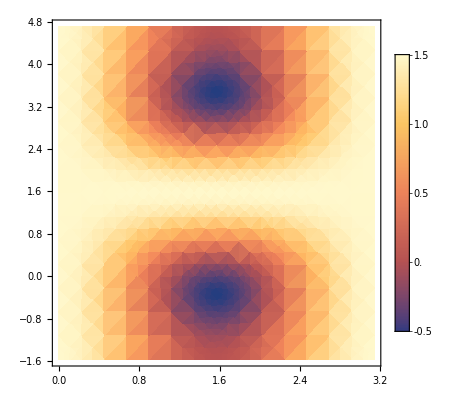

```mathematica
DensityPlot[3/32 (9+7 Cos[2 t]+2 Sin[t]^2 (-3 Cos[2 ϕ11]+4 Sin[ϕ11])),{t,0,(2Pi)/2},{ϕ11,-Pi/2,(3Pi)/2},PlotLegends->Automatic]
```

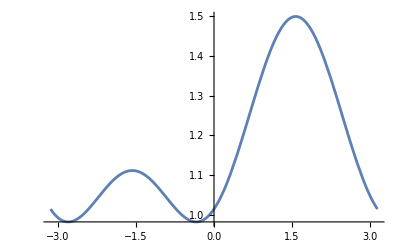

```mathematica
t=0.534;
Plot[3/32 (9+7 Cos[2 t]+2 Sin[t]^2 (-3 Cos[2 ϕ11]+4 Sin[ϕ11])),{ϕ11,-Pi,Pi}]
```

```mathematica
ConjuTranst3half2.Iz3half2.st3half2//FullSimplify
```

{{0}}

```mathematica
StateEvo[ϕ11,ϕ2,ϕ3,t,θ,ϕ]//FullSimplify
```

```mathematica
st3half2ALL={{1/32 ⅇ^(-1/2 ⅈ (3 t+2 (ϕ11+ϕ2+ϕ3))) Sin[θ/2]^3 (-4 ⅇ^(3 ⅈ ϕ) (-1+ⅇ^(ⅈ t))^3+4 ⅇ^(ⅈ ϕ3) (1+ⅇ^(ⅈ t)) Cot[θ/2] (3 ⅇ^(2 ⅈ ϕ) (-1+ⅇ^(ⅈ t))^2+6 Cot[θ/2] Sin[t] (-ⅈ Cos[t+ϕ+ϕ2]+Sin[t+ϕ+ϕ2])+4 Cos[t/2]^2 Cot[θ/2]^2 (Cos[t+ϕ11+ϕ2]+ⅈ Sin[t+ϕ11+ϕ2])))},{1/32 √3 ⅇ^(-1/2 ⅈ (3 t+2 (ϕ2+ϕ3))) (4 ⅇ^(3 ⅈ ϕ) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t))+4 ⅇ^(ⅈ ϕ3) Cot[θ/2] (ⅇ^(2 ⅈ ϕ) (3-ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)-3 ⅇ^(3 ⅈ t))+ⅇ^(ⅈ (ϕ+ϕ2)) (3+ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t)) Cot[θ/2]-ⅇ^(ⅈ (ϕ11+ϕ2)) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2 Cot[θ/2]^2)) Sin[θ/2]^3},{1/32 √3 ⅇ^(-1/2 ⅈ (3 t+2 ϕ3)) (-4 ⅇ^(3 ⅈ ϕ) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2+4 ⅇ^(ⅈ (2 ϕ+ϕ3)) (3+ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t)) Cot[θ/2]-4 ⅇ^(ⅈ (ϕ+ϕ2+ϕ3)) (-3+ⅇ^(ⅈ t)-ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t)) Cot[θ/2]^2+4 ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t)) Cot[θ/2]^3) Sin[θ/2]^3},{1/32 ⅇ^(-(3 ⅈ t)/2) Sin[θ/2]^3 (4 ⅇ^(3 ⅈ ϕ) (1+ⅇ^(ⅈ t))^3+4 ⅇ^(ⅈ ϕ3) (-1+ⅇ^(ⅈ t)) Cot[θ/2] (-3 ⅇ^(2 ⅈ ϕ) (1+ⅇ^(ⅈ t))^2+6 ⅈ Cot[θ/2] Sin[t] (Cos[t+ϕ+ϕ2]+ⅈ Sin[t+ϕ+ϕ2])+4 Cot[θ/2]^2 Sin[t/2]^2 (Cos[t+ϕ11+ϕ2]+ⅈ Sin[t+ϕ11+ϕ2])))}};
```

```mathematica
ConjugateTranspose[st3half2ALL]
```

```mathematica
ConTranst3half2ALL={{1/32 ⅇ^(1/2 ⅈ (3 t+2 (ϕ11+ϕ2+ϕ3))) (-4 ⅇ^(3 (-ⅈ) ϕ) (-1+ⅇ^((-ⅈ) t))^3+4 ⅇ^((-ⅈ) ϕ3) (1+ⅇ^((-ⅈ) t)) Cot[θ/2] (3 ⅇ^(2 (-ⅈ) ϕ) (-1+ⅇ^((-ⅈ) t))^2+6 Cot[θ/2] Sin[t] (-(-ⅈ) Cos[t+ϕ+ϕ2]+Sin[t+ϕ+ϕ2])+4 Cos[t/2]^2 Cot[θ/2]^2 (Cos[t+ϕ11+ϕ2]+(-ⅈ) Sin[t+ϕ11+ϕ2]))) Sin[θ/2]^3,1/32 √3 ⅇ^(1/2 ⅈ (3 t+2 (ϕ2+ϕ3))) (4 ⅇ^(3 (-ⅈ) ϕ) (-1+ⅇ^((-ⅈ) t))^2 (1+ⅇ^((-ⅈ) t))+4 ⅇ^((-ⅈ) ϕ3) Cot[θ/2] (ⅇ^(2 (-ⅈ) ϕ) (3-ⅇ^((-ⅈ) t)+ⅇ^(2 (-ⅈ) t)-3 ⅇ^(3 (-ⅈ) t))+ⅇ^((-ⅈ) (ϕ+ϕ2)) (3+ⅇ^((-ⅈ) t)+ⅇ^(2 (-ⅈ) t)+3 ⅇ^(3 (-ⅈ) t)) Cot[θ/2]-ⅇ^((-ⅈ) (ϕ11+ϕ2)) (-1+ⅇ^((-ⅈ) t)) (1+ⅇ^((-ⅈ) t))^2 Cot[θ/2]^2)) Sin[θ/2]^3,1/32 √3 ⅇ^(1/2 ⅈ (3 t+2 ϕ3)) (-4 ⅇ^(3 (-ⅈ) ϕ) (-1+ⅇ^((-ⅈ) t)) (1+ⅇ^((-ⅈ) t))^2+4 ⅇ^((-ⅈ) (2 ϕ+ϕ3)) (3+ⅇ^((-ⅈ) t)+ⅇ^(2 (-ⅈ) t)+3 ⅇ^(3 (-ⅈ) t)) Cot[θ/2]-4 ⅇ^((-ⅈ) (ϕ+ϕ2+ϕ3)) (-3+ⅇ^((-ⅈ) t)-ⅇ^(2 (-ⅈ) t)+3 ⅇ^(3 (-ⅈ) t)) Cot[θ/2]^2+4 ⅇ^((-ⅈ) (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^((-ⅈ) t))^2 (1+ⅇ^((-ⅈ) t)) Cot[θ/2]^3) Sin[θ/2]^3,1/32 ⅇ^(3/2 ⅈ t) (4 ⅇ^(3 (-ⅈ) ϕ) (1+ⅇ^((-ⅈ) t))^3+4 ⅇ^((-ⅈ) ϕ3) (-1+ⅇ^((-ⅈ) t)) Cot[θ/2] (-3 ⅇ^(2 (-ⅈ) ϕ) (1+ⅇ^((-ⅈ) t))^2+6 (-ⅈ) Cot[θ/2] Sin[t] (Cos[t+ϕ+ϕ2]+(-ⅈ) Sin[t+ϕ+ϕ2])+4 Cot[θ/2]^2 Sin[t/2]^2 (Cos[t+ϕ11+ϕ2]+(-ⅈ) Sin[t+ϕ11+ϕ2]))) Sin[θ/2]^3}};
```

```mathematica
ConTranst3half2ALL.Ix3half2.st3half2ALL//FullSimplify
```

{{1/32 √3 ⅇ^(-1/2 ⅈ (3 t+2 (ϕ2+ϕ3))) (4 ⅇ^(3 ⅈ ϕ) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t))+4 ⅇ^(ⅈ ϕ3) Cot[θ/2] (ⅇ^(2 ⅈ ϕ) (3-ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)-3 ⅇ^(3 ⅈ t))+ⅇ^(ⅈ (ϕ+ϕ2)) (3+ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t)) Cot[θ/2]-ⅇ^(ⅈ (ϕ11+ϕ2)) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2 Cot[θ/2]^2)) Sin[θ/2]^3 (1/32 √3 ⅇ^(1/2 ⅈ (3 t+2 ϕ3)) (-4 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(-ⅈ t)) (1+ⅇ^(-ⅈ t))^2+4 ⅇ^(-ⅈ (2 ϕ+ϕ3)) (3+ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]-4 ⅇ^(-ⅈ (ϕ+ϕ2+ϕ3)) (-3+ⅇ^(-ⅈ t)-ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]^2+4 ⅇ^(-ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(-ⅈ t))^2 (1+ⅇ^(-ⅈ t)) Cot[θ/2]^3) Sin[θ/2]^3+1/64 √3 ⅇ^(1/2 ⅈ (3 t+2 (ϕ11+ϕ2+ϕ3))) Sin[θ/2]^3 (-4 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(-ⅈ t))^3+4 ⅇ^(-ⅈ ϕ3) (1+ⅇ^(-ⅈ t)) Cot[θ/2] (3 ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(-ⅈ t))^2+6 Cot[θ/2] Sin[t] (ⅈ Cos[t+ϕ+ϕ2]+Sin[t+ϕ+ϕ2])+4 Cos[t/2]^2 Cot[θ/2]^2 (Cos[t+ϕ11+ϕ2]-ⅈ Sin[t+ϕ11+ϕ2]))))+1/32 √3 ⅇ^(-1/2 ⅈ (3 t+2 ϕ3)) (-4 ⅇ^(3 ⅈ ϕ) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2+4 ⅇ^(ⅈ (2 ϕ+ϕ3)) (3+ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t)) Cot[θ/2]-4 ⅇ^(ⅈ (ϕ+ϕ2+ϕ3)) (-3+ⅇ^(ⅈ t)-ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t)) Cot[θ/2]^2+4 ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t)) Cot[θ/2]^3) Sin[θ/2]^3 (1/32 √3 ⅇ^(1/2 ⅈ (3 t+2 (ϕ2+ϕ3))) (4 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(-ⅈ t))^2 (1+ⅇ^(-ⅈ t))+4 ⅇ^(-ⅈ ϕ3) Cot[θ/2] (ⅇ^(-2 ⅈ ϕ) (3-ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)-3 ⅇ^(-3 ⅈ t))+ⅇ^(-ⅈ (ϕ+ϕ2)) (3+ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]-ⅇ^(-ⅈ (ϕ11+ϕ2)) (-1+ⅇ^(-ⅈ t)) (1+ⅇ^(-ⅈ t))^2 Cot[θ/2]^2)) Sin[θ/2]^3+1/64 √3 ⅇ^((3 ⅈ t)/2) Sin[θ/2]^3 (4 ⅇ^(-3 ⅈ ϕ) (1+ⅇ^(-ⅈ t))^3+4 ⅇ^(-ⅈ ϕ3) (-1+ⅇ^(-ⅈ t)) Cot[θ/2] (-3 ⅇ^(-2 ⅈ ϕ) (1+ⅇ^(-ⅈ t))^2-6 ⅈ Cot[θ/2] Sin[t] (Cos[t+ϕ+ϕ2]-ⅈ Sin[t+ϕ+ϕ2])+4 Cot[θ/2]^2 Sin[t/2]^2 (Cos[t+ϕ11+ϕ2]-ⅈ Sin[t+ϕ11+ϕ2]))))+1/2048 3 ⅇ^(1/2 ⅈ (3 t+2 (ϕ2+ϕ3))-1/2 ⅈ (3 t+2 (ϕ11+ϕ2+ϕ3))) (4 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(-ⅈ t))^2 (1+ⅇ^(-ⅈ t))+4 ⅇ^(-ⅈ ϕ3) Cot[θ/2] (ⅇ^(-2 ⅈ ϕ) (3-ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)-3 ⅇ^(-3 ⅈ t))+ⅇ^(-ⅈ (ϕ+ϕ2)) (3+ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]-ⅇ^(-ⅈ (ϕ11+ϕ2)) (-1+ⅇ^(-ⅈ t)) (1+ⅇ^(-ⅈ t))^2 Cot[θ/2]^2)) Sin[θ/2]^6 (-4 ⅇ^(3 ⅈ ϕ) (-1+ⅇ^(ⅈ t))^3+4 ⅇ^(ⅈ ϕ3) (1+ⅇ^(ⅈ t)) Cot[θ/2] (3 ⅇ^(2 ⅈ ϕ) (-1+ⅇ^(ⅈ t))^2+6 Cot[θ/2] Sin[t] (-ⅈ Cos[t+ϕ+ϕ2]+Sin[t+ϕ+ϕ2])+4 Cos[t/2]^2 Cot[θ/2]^2 (Cos[t+ϕ11+ϕ2]+ⅈ Sin[t+ϕ11+ϕ2])))+1/2048 3 ⅇ^(-(3 ⅈ t)/2+1/2 ⅈ (3 t+2 ϕ3)) (-4 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(-ⅈ t)) (1+ⅇ^(-ⅈ t))^2+4 ⅇ^(-ⅈ (2 ϕ+ϕ3)) (3+ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]-4 ⅇ^(-ⅈ (ϕ+ϕ2+ϕ3)) (-3+ⅇ^(-ⅈ t)-ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]^2+4 ⅇ^(-ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(-ⅈ t))^2 (1+ⅇ^(-ⅈ t)) Cot[θ/2]^3) Sin[θ/2]^6 (4 ⅇ^(3 ⅈ ϕ) (1+ⅇ^(ⅈ t))^3+4 ⅇ^(ⅈ ϕ3) (-1+ⅇ^(ⅈ t)) Cot[θ/2] (-3 ⅇ^(2 ⅈ ϕ) (1+ⅇ^(ⅈ t))^2+6 ⅈ Cot[θ/2] Sin[t] (Cos[t+ϕ+ϕ2]+ⅈ Sin[t+ϕ+ϕ2])+4 Cot[θ/2]^2 Sin[t/2]^2 (Cos[t+ϕ11+ϕ2]+ⅈ Sin[t+ϕ11+ϕ2])))}}

```mathematica
ConTranst3half2ALL.Iy3half2.st3half2ALL//FullSimplify
```

{{1/32 √3 ⅇ^(-1/2 ⅈ (3 t+2 (ϕ2+ϕ3))) (4 ⅇ^(3 ⅈ ϕ) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t))+4 ⅇ^(ⅈ ϕ3) Cot[θ/2] (ⅇ^(2 ⅈ ϕ) (3-ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)-3 ⅇ^(3 ⅈ t))+ⅇ^(ⅈ (ϕ+ϕ2)) (3+ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t)) Cot[θ/2]-ⅇ^(ⅈ (ϕ11+ϕ2)) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2 Cot[θ/2]^2)) Sin[θ/2]^3 (1/32 ⅈ √3 ⅇ^(1/2 ⅈ (3 t+2 ϕ3)) (-4 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(-ⅈ t)) (1+ⅇ^(-ⅈ t))^2+4 ⅇ^(-ⅈ (2 ϕ+ϕ3)) (3+ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]-4 ⅇ^(-ⅈ (ϕ+ϕ2+ϕ3)) (-3+ⅇ^(-ⅈ t)-ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]^2+4 ⅇ^(-ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(-ⅈ t))^2 (1+ⅇ^(-ⅈ t)) Cot[θ/2]^3) Sin[θ/2]^3-1/64 ⅈ √3 ⅇ^(1/2 ⅈ (3 t+2 (ϕ11+ϕ2+ϕ3))) Sin[θ/2]^3 (-4 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(-ⅈ t))^3+4 ⅇ^(-ⅈ ϕ3) (1+ⅇ^(-ⅈ t)) Cot[θ/2] (3 ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(-ⅈ t))^2+6 Cot[θ/2] Sin[t] (ⅈ Cos[t+ϕ+ϕ2]+Sin[t+ϕ+ϕ2])+4 Cos[t/2]^2 Cot[θ/2]^2 (Cos[t+ϕ11+ϕ2]-ⅈ Sin[t+ϕ11+ϕ2]))))+1/32 √3 ⅇ^(-1/2 ⅈ (3 t+2 ϕ3)) (-4 ⅇ^(3 ⅈ ϕ) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2+4 ⅇ^(ⅈ (2 ϕ+ϕ3)) (3+ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t)) Cot[θ/2]-4 ⅇ^(ⅈ (ϕ+ϕ2+ϕ3)) (-3+ⅇ^(ⅈ t)-ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t)) Cot[θ/2]^2+4 ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t)) Cot[θ/2]^3) Sin[θ/2]^3 (-1/32 ⅈ √3 ⅇ^(1/2 ⅈ (3 t+2 (ϕ2+ϕ3))) (4 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(-ⅈ t))^2 (1+ⅇ^(-ⅈ t))+4 ⅇ^(-ⅈ ϕ3) Cot[θ/2] (ⅇ^(-2 ⅈ ϕ) (3-ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)-3 ⅇ^(-3 ⅈ t))+ⅇ^(-ⅈ (ϕ+ϕ2)) (3+ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]-ⅇ^(-ⅈ (ϕ11+ϕ2)) (-1+ⅇ^(-ⅈ t)) (1+ⅇ^(-ⅈ t))^2 Cot[θ/2]^2)) Sin[θ/2]^3+1/64 ⅈ √3 ⅇ^((3 ⅈ t)/2) Sin[θ/2]^3 (4 ⅇ^(-3 ⅈ ϕ) (1+ⅇ^(-ⅈ t))^3+4 ⅇ^(-ⅈ ϕ3) (-1+ⅇ^(-ⅈ t)) Cot[θ/2] (-3 ⅇ^(-2 ⅈ ϕ) (1+ⅇ^(-ⅈ t))^2-6 ⅈ Cot[θ/2] Sin[t] (Cos[t+ϕ+ϕ2]-ⅈ Sin[t+ϕ+ϕ2])+4 Cot[θ/2]^2 Sin[t/2]^2 (Cos[t+ϕ11+ϕ2]-ⅈ Sin[t+ϕ11+ϕ2]))))+1/2048 3 ⅈ ⅇ^(1/2 ⅈ (3 t+2 (ϕ2+ϕ3))-1/2 ⅈ (3 t+2 (ϕ11+ϕ2+ϕ3))) (4 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(-ⅈ t))^2 (1+ⅇ^(-ⅈ t))+4 ⅇ^(-ⅈ ϕ3) Cot[θ/2] (ⅇ^(-2 ⅈ ϕ) (3-ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)-3 ⅇ^(-3 ⅈ t))+ⅇ^(-ⅈ (ϕ+ϕ2)) (3+ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]-ⅇ^(-ⅈ (ϕ11+ϕ2)) (-1+ⅇ^(-ⅈ t)) (1+ⅇ^(-ⅈ t))^2 Cot[θ/2]^2)) Sin[θ/2]^6 (-4 ⅇ^(3 ⅈ ϕ) (-1+ⅇ^(ⅈ t))^3+4 ⅇ^(ⅈ ϕ3) (1+ⅇ^(ⅈ t)) Cot[θ/2] (3 ⅇ^(2 ⅈ ϕ) (-1+ⅇ^(ⅈ t))^2+6 Cot[θ/2] Sin[t] (-ⅈ Cos[t+ϕ+ϕ2]+Sin[t+ϕ+ϕ2])+4 Cos[t/2]^2 Cot[θ/2]^2 (Cos[t+ϕ11+ϕ2]+ⅈ Sin[t+ϕ11+ϕ2])))-1/2048 3 ⅈ ⅇ^(-(3 ⅈ t)/2+1/2 ⅈ (3 t+2 ϕ3)) (-4 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(-ⅈ t)) (1+ⅇ^(-ⅈ t))^2+4 ⅇ^(-ⅈ (2 ϕ+ϕ3)) (3+ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]-4 ⅇ^(-ⅈ (ϕ+ϕ2+ϕ3)) (-3+ⅇ^(-ⅈ t)-ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]^2+4 ⅇ^(-ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(-ⅈ t))^2 (1+ⅇ^(-ⅈ t)) Cot[θ/2]^3) Sin[θ/2]^6 (4 ⅇ^(3 ⅈ ϕ) (1+ⅇ^(ⅈ t))^3+4 ⅇ^(ⅈ ϕ3) (-1+ⅇ^(ⅈ t)) Cot[θ/2] (-3 ⅇ^(2 ⅈ ϕ) (1+ⅇ^(ⅈ t))^2+6 ⅈ Cot[θ/2] Sin[t] (Cos[t+ϕ+ϕ2]+ⅈ Sin[t+ϕ+ϕ2])+4 Cot[θ/2]^2 Sin[t/2]^2 (Cos[t+ϕ11+ϕ2]+ⅈ Sin[t+ϕ11+ϕ2])))}}

```mathematica
ConTranst3half2ALL.Iz3half2.st3half2ALL//FullSimplify
```

{{-1/2048 3 (-4 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(-ⅈ t)) (1+ⅇ^(-ⅈ t))^2+4 ⅇ^(-ⅈ (2 ϕ+ϕ3)) (3+ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]-4 ⅇ^(-ⅈ (ϕ+ϕ2+ϕ3)) (-3+ⅇ^(-ⅈ t)-ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]^2+4 ⅇ^(-ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(-ⅈ t))^2 (1+ⅇ^(-ⅈ t)) Cot[θ/2]^3) (-4 ⅇ^(3 ⅈ ϕ) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2+4 ⅇ^(ⅈ (2 ϕ+ϕ3)) (3+ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t)) Cot[θ/2]-4 ⅇ^(ⅈ (ϕ+ϕ2+ϕ3)) (-3+ⅇ^(ⅈ t)-ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t)) Cot[θ/2]^2+4 ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t)) Cot[θ/2]^3) Sin[θ/2]^6+1/2048 3 (4 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(-ⅈ t))^2 (1+ⅇ^(-ⅈ t))+4 ⅇ^(-ⅈ ϕ3) Cot[θ/2] (ⅇ^(-2 ⅈ ϕ) (3-ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)-3 ⅇ^(-3 ⅈ t))+ⅇ^(-ⅈ (ϕ+ϕ2)) (3+ⅇ^(-ⅈ t)+ⅇ^(-2 ⅈ t)+3 ⅇ^(-3 ⅈ t)) Cot[θ/2]-ⅇ^(-ⅈ (ϕ11+ϕ2)) (-1+ⅇ^(-ⅈ t)) (1+ⅇ^(-ⅈ t))^2 Cot[θ/2]^2)) (4 ⅇ^(3 ⅈ ϕ) (-1+ⅇ^(ⅈ t))^2 (1+ⅇ^(ⅈ t))+4 ⅇ^(ⅈ ϕ3) Cot[θ/2] (ⅇ^(2 ⅈ ϕ) (3-ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)-3 ⅇ^(3 ⅈ t))+ⅇ^(ⅈ (ϕ+ϕ2)) (3+ⅇ^(ⅈ t)+ⅇ^(2 ⅈ t)+3 ⅇ^(3 ⅈ t)) Cot[θ/2]-ⅇ^(ⅈ (ϕ11+ϕ2)) (-1+ⅇ^(ⅈ t)) (1+ⅇ^(ⅈ t))^2 Cot[θ/2]^2)) Sin[θ/2]^6+1/2048 3 Sin[θ/2]^6 (-4 ⅇ^(-3 ⅈ ϕ) (-1+ⅇ^(-ⅈ t))^3+4 ⅇ^(-ⅈ ϕ3) (1+ⅇ^(-ⅈ t)) Cot[θ/2] (3 ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(-ⅈ t))^2+6 Cot[θ/2] Sin[t] (ⅈ Cos[t+ϕ+ϕ2]+Sin[t+ϕ+ϕ2])+4 Cos[t/2]^2 Cot[θ/2]^2 (Cos[t+ϕ11+ϕ2]-ⅈ Sin[t+ϕ11+ϕ2]))) (-4 ⅇ^(3 ⅈ ϕ) (-1+ⅇ^(ⅈ t))^3+4 ⅇ^(ⅈ ϕ3) (1+ⅇ^(ⅈ t)) Cot[θ/2] (3 ⅇ^(2 ⅈ ϕ) (-1+ⅇ^(ⅈ t))^2+6 Cot[θ/2] Sin[t] (-ⅈ Cos[t+ϕ+ϕ2]+Sin[t+ϕ+ϕ2])+4 Cos[t/2]^2 Cot[θ/2]^2 (Cos[t+ϕ11+ϕ2]+ⅈ Sin[t+ϕ11+ϕ2])))-1/2048 3 Sin[θ/2]^6 (4 ⅇ^(-3 ⅈ ϕ) (1+ⅇ^(-ⅈ t))^3+4 ⅇ^(-ⅈ ϕ3) (-1+ⅇ^(-ⅈ t)) Cot[θ/2] (-3 ⅇ^(-2 ⅈ ϕ) (1+ⅇ^(-ⅈ t))^2-6 ⅈ Cot[θ/2] Sin[t] (Cos[t+ϕ+ϕ2]-ⅈ Sin[t+ϕ+ϕ2])+4 Cot[θ/2]^2 Sin[t/2]^2 (Cos[t+ϕ11+ϕ2]-ⅈ Sin[t+ϕ11+ϕ2]))) (4 ⅇ^(3 ⅈ ϕ) (1+ⅇ^(ⅈ t))^3+4 ⅇ^(ⅈ ϕ3) (-1+ⅇ^(ⅈ t)) Cot[θ/2] (-3 ⅇ^(2 ⅈ ϕ) (1+ⅇ^(ⅈ t))^2+6 ⅈ Cot[θ/2] Sin[t] (Cos[t+ϕ+ϕ2]+ⅈ Sin[t+ϕ+ϕ2])+4 Cot[θ/2]^2 Sin[t/2]^2 (Cos[t+ϕ11+ϕ2]+ⅈ Sin[t+ϕ11+ϕ2])))}}

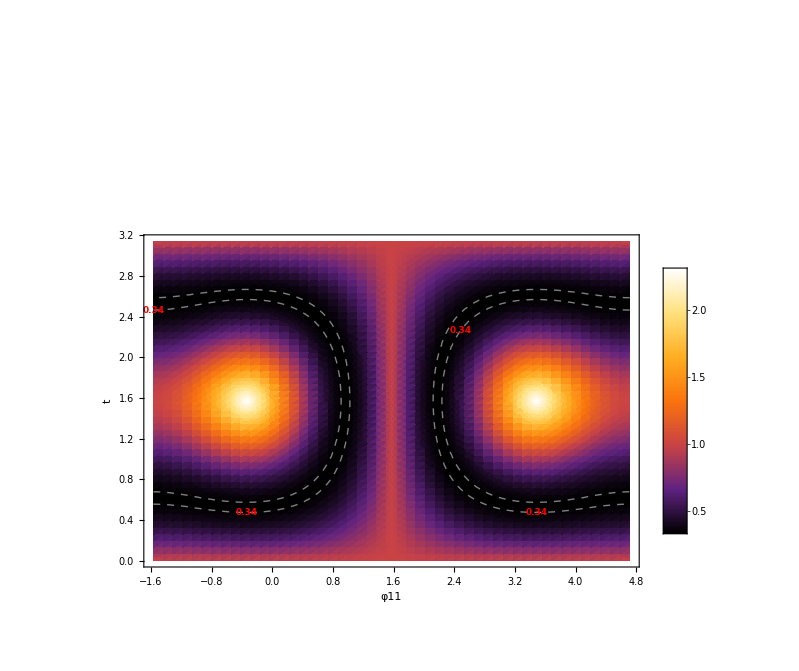

```mathematica
AA2=Show[(*主密度图-保持完整显示*)DensityPlot[ξSqure[Chop[N[StateEvo[ϕ11,Pi/2,Pi-ϕ11,t,Pi/2,Pi/2]]]]/(3/2),{ϕ11,-Pi/2,(3Pi)/2},{t,0,Pi},PlotLegends->Automatic,ColorFunction->"SunsetColors",PlotPoints->50,FrameLabel->{"φ11","t"},LabelStyle->{Bold,12}],(*青色区域:仅填充<0.25 区域，不遮挡其他部分*)ContourPlot[ξSqure[Chop[N[StateEvo[ϕ11,Pi/2,Pi-ϕ11,t,Pi/2,Pi/2]]]]/(3/2),{ϕ11,-Pi/2,(3Pi)/2},{t,0,2Pi},Contours->Range[0.3,0.34,0.01],(*仅<0.5 的等高线值*)ContourLabels->(Text[Style[#3,9,Bold,Red],{#1,#2}]&),(*红色标签*)ContourStyle->Directive[Gray,Thick,Dashed],(*黑色虚线*)PlotPoints->50,ContourShading->None  (*🔥 关键修复:禁用背景填充!*)]]
```

```mathematica
Export["D:\\desksave2\\Astro\\spin squeezing\\picture save\\Density3half2new.pdf",AA2]
```

D:\desksave2\Astro\spin squeezing\picture save\Density3half2new.pdf

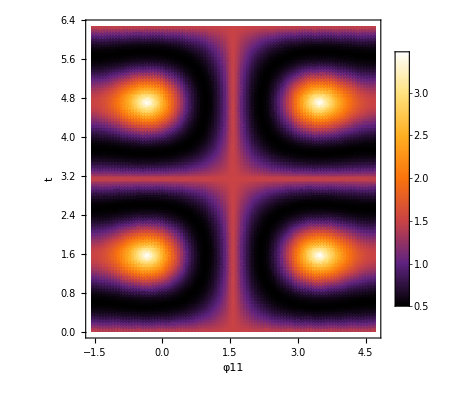

```mathematica
DensityPlot[ξSqure[Chop[N[StateEvo[ϕ11,Pi/2,Pi-ϕ11,t,Pi/2,Pi/2]]]],{ϕ11,-Pi/2,(3Pi)/2},{t,0,2Pi},PlotLegends->Automatic,ColorFunction->"SunsetColors",PlotPoints->100,FrameLabel->{"φ11","t"},LabelStyle->{Bold,12}]
```

```mathematica
.
```

```mathematica
MatrixExp[-I*Hmuti[ϕ1,ϕ2,ϕ3]*t].StateθϕInitial[Pi/2,Pi/2]//FullSimplify
```

```mathematica
MatrixExp[-I*Hmuti[Pi-ϕ,Pi/2,ϕ]*t].StateθϕInitial[Pi/2,Pi/2]//FullSimplify
```

{{(ⅇ^(-(3 ⅈ t)/2) (1+3 ⅇ^(2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]+ⅈ Sin[t+ϕ])))/(8 √2)},{1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(2 ⅈ t)+ⅈ ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t)))},{-1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t])},{(ⅇ^(-(3 ⅈ t)/2) (3 ⅇ^(ⅈ ϕ) (-1+ⅇ^(2 ⅈ t))-ⅈ (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}}

```mathematica
st1={{(ⅇ^(-(3 ⅈ t)/2) (1+3 ⅇ^(2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]+ⅈ Sin[t+ϕ])))/(8 √2)},{1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(2 ⅈ t)+ⅈ ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t)))},{-1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t])},{(ⅇ^(-(3 ⅈ t)/2) (3 ⅇ^(ⅈ ϕ) (-1+ⅇ^(2 ⅈ t))-ⅈ (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}};
```

```mathematica
ConjugateTranspose[st1].Iy3half2.st1//FullSimplify
```

{{3/256 ⅇ^(-ⅈ (t+Re[t])) (2 (1+3 ⅇ^(2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]+ⅈ Sin[t+ϕ])) (1+3 ⅇ^(2 ⅈ Conjugate[t])+2 ⅇ^(ⅈ (Conjugate[t]+Conjugate[ϕ])) Sin[Conjugate[t]])+2 ⅇ^(-ⅈ (ϕ-Conjugate[t])) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅈ Sin[t]^2+Sin[2 t]) (6 Cos[Conjugate[t]]+Sin[Conjugate[t]] (ⅈ-Cos[Conjugate[ϕ]]+5 ⅈ Sin[Conjugate[ϕ]]))+ⅇ^(-ⅈ ϕ) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t]) (5+7 ⅇ^(2 ⅈ Conjugate[t])+(-1+ⅇ^(2 ⅈ Conjugate[t])) (ⅈ Cos[Conjugate[ϕ]]+5 Sin[Conjugate[ϕ]])))}}

```mathematica
{{3/256 ⅇ^(-ⅈ (t+t)) (2 (1+3 ⅇ^(2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]+ⅈ Sin[t+ϕ])) (1+3 ⅇ^(2 ⅈ t)+2 ⅇ^(ⅈ (t+ϕ)) Sin[t])+2 ⅇ^(-ⅈ (ϕ-t)) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅈ Sin[t]^2+Sin[2 t]) (6 Cos[t]+Sin[t] (ⅈ-Cos[ϕ]+5 ⅈ Sin[ϕ]))+ⅇ^(-ⅈ ϕ) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t]) (5+7 ⅇ^(2 ⅈ t)+(-1+ⅇ^(2 ⅈ t)) (ⅈ Cos[ϕ]+5 Sin[ϕ])))}}//FullSimplify
```

{{3/32 (9+7 Cos[2 t]+2 Sin[t]^2 (-3 Cos[2 ϕ]+4 Sin[ϕ]))}}

```mathematica
T[ϕ_,t_]:=3/32 (9+7 Cos[2 t]+2 Sin[t]^2 (-3 Cos[2 ϕ]+4 Sin[ϕ]))
```

```mathematica
T[ϕ,0.513]
```

3/32 (12.6277+0.481756 (-3 Cos[2 ϕ]+4 Sin[ϕ]))

```mathematica
θ111[state1_]:=Module[{st=state1},
xVal=0;
yVal={{3/32 (9+7 Cos[2 t]+2 Sin[t]^2 (-3 Cos[2 ϕ]+4 Sin[ϕ]))}};
zVal=0;
First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]
]
ϕ111[state1_]:=Module[{st=state1},
xVal=0;
yVal={{3/32 (9+7 Cos[2 t]+2 Sin[t]^2 (-3 Cos[2 ϕ]+4 Sin[ϕ]))}};
zVal=0;
First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]
(*If[First[Flatten[yVal]]>0,First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]],2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]*)
]

In1[state_]:=-Ix3half2*Sin[ϕ111[state]]+Iy3half2*Cos[ϕ111[state]]
In2[state_]:=-Ix3half2*Cos[θ1[state]]Cos[ϕ111[state]]-Iy3half2*Cos[θ111[state]]Sin[ϕ111[state]]+Iz3half2*Sin[θ111[state]]
In1n2plusSqure[state_]:=ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state
In1n2minusSqure[state_]:=ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state
In1n2n2n1[state_]:=ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state
ξSqure[state_]:=First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]
```

```mathematica
ξSqure[{{(ⅇ^(-(3 ⅈ t)/2) (1+3 ⅇ^(2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]+ⅈ Sin[t+ϕ])))/(8 √2)},{1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(2 ⅈ t)+ⅈ ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t)))},{-1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t])},{(ⅇ^(-(3 ⅈ t)/2) (3 ⅇ^(ⅈ ϕ) (-1+ⅇ^(2 ⅈ t))-ⅈ (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}}]
```

```mathematica
st22=1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(2 ⅈ t)+ⅈ ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))) (1/4 √(3/2) ⅇ^(1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(-2 ⅈ t)-ⅈ ⅇ^(-ⅈ ϕ) (3+ⅇ^(-2 ⅈ t)))+1/16 √(3/2) ⅇ^(3/2 ⅈ t) (3 ⅇ^(-ⅈ ϕ) (-1+ⅇ^(-2 ⅈ t))+ⅈ (1+3 ⅇ^(-2 ⅈ t))))+(ⅇ^(-(3 ⅈ t)/2) (3 ⅇ^(ⅈ ϕ) (-1+ⅇ^(2 ⅈ t))-ⅈ (1+3 ⅇ^(2 ⅈ t))) ((3 ⅇ^(1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(-2 ⅈ t)-ⅈ ⅇ^(-ⅈ ϕ) (3+ⅇ^(-2 ⅈ t))))/(16 √2)+(3 ⅇ^(3/2 ⅈ t) (3 ⅇ^(-ⅈ ϕ) (-1+ⅇ^(-2 ⅈ t))+ⅈ (1+3 ⅇ^(-2 ⅈ t))))/(8 √2)))/(8 √2)-1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (-1/4 √(3/2) ⅇ^(1/2 ⅈ (3 t+2 ϕ)) Conjugate[ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t]]+1/16 √(3/2) ⅇ^(3/2 ⅈ t) (1+3 ⅇ^(-2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]-ⅈ Sin[t+ϕ]))) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t])-√((-3/128 ⅇ^(-(3 ⅈ t)/2+1/2 ⅈ (3 t+2 ϕ)) (3 ⅇ^(ⅈ ϕ) (-1+ⅇ^(2 ⅈ t))-ⅈ (1+3 ⅇ^(2 ⅈ t))) Conjugate[ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t]]-3/128 ⅇ^(-1/2 ⅈ (3 t+2 ϕ)+3/2 ⅈ t) (-1+ⅇ^(2 ⅈ t)+ⅈ ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))) (1+3 ⅇ^(-2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]-ⅈ Sin[t+ϕ]))-3/128 ⅇ^(-1/2 ⅈ (3 t+2 ϕ)+3/2 ⅈ t) (3 ⅇ^(-ⅈ ϕ) (-1+ⅇ^(-2 ⅈ t))+ⅈ (1+3 ⅇ^(-2 ⅈ t))) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t])-3/128 ⅇ^(-(3 ⅈ t)/2+1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(-2 ⅈ t)-ⅈ ⅇ^(-ⅈ ϕ) (3+ⅇ^(-2 ⅈ t))) (1+3 ⅇ^(2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]+ⅈ Sin[t+ϕ])))^2+(1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(2 ⅈ t)+ⅈ ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))) (3/16 √(3/2) ⅇ^(1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(-2 ⅈ t)-ⅈ ⅇ^(-ⅈ ϕ) (3+ⅇ^(-2 ⅈ t)))+1/16 √(3/2) ⅇ^(3/2 ⅈ t) (3 ⅇ^(-ⅈ ϕ) (-1+ⅇ^(-2 ⅈ t))+ⅈ (1+3 ⅇ^(-2 ⅈ t))))+(ⅇ^(-(3 ⅈ t)/2) (3 ⅇ^(ⅈ ϕ) (-1+ⅇ^(2 ⅈ t))-ⅈ (1+3 ⅇ^(2 ⅈ t))) ((3 ⅇ^(1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(-2 ⅈ t)-ⅈ ⅇ^(-ⅈ ϕ) (3+ⅇ^(-2 ⅈ t))))/(16 √2)-(3 ⅇ^(3/2 ⅈ t) (3 ⅇ^(-ⅈ ϕ) (-1+ⅇ^(-2 ⅈ t))+ⅈ (1+3 ⅇ^(-2 ⅈ t))))/(16 √2)))/(8 √2)-1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (-3/16 √(3/2) ⅇ^(1/2 ⅈ (3 t+2 ϕ)) Conjugate[ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t]]+1/16 √(3/2) ⅇ^(3/2 ⅈ t) (1+3 ⅇ^(-2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]-ⅈ Sin[t+ϕ]))) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t])+(ⅇ^(-(3 ⅈ t)/2) (-(3 ⅇ^(1/2 ⅈ (3 t+2 ϕ)) Conjugate[ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t]])/(16 √2)-(3 ⅇ^(3/2 ⅈ t) (1+3 ⅇ^(-2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]-ⅈ Sin[t+ϕ])))/(16 √2)) (1+3 ⅇ^(2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]+ⅈ Sin[t+ϕ])))/(8 √2))^2)+(ⅇ^(-(3 ⅈ t)/2) (-(3 ⅇ^(1/2 ⅈ (3 t+2 ϕ)) Conjugate[ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t]])/(16 √2)+(3 ⅇ^(3/2 ⅈ t) (1+3 ⅇ^(-2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]-ⅈ Sin[t+ϕ])))/(8 √2)) (1+3 ⅇ^(2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]+ⅈ Sin[t+ϕ])))/(8 √2);
```

```mathematica
st22//FullSimplify
```

```mathematica
st33=1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(2 ⅈ t)+ⅈ ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))) (1/4 √(3/2) ⅇ^(1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(-2 ⅈ t)-ⅈ ⅇ^(-ⅈ ϕ) (3+ⅇ^(-2 ⅈ t)))+1/16 √(3/2) ⅇ^(3/2 ⅈ t) (3 ⅇ^(-ⅈ ϕ) (-1+ⅇ^(-2 ⅈ t))+ⅈ (1+3 ⅇ^(-2 ⅈ t))))+(ⅇ^(-(3 ⅈ t)/2) (3 ⅇ^(ⅈ ϕ) (-1+ⅇ^(2 ⅈ t))-ⅈ (1+3 ⅇ^(2 ⅈ t))) ((3 ⅇ^(1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(-2 ⅈ t)-ⅈ ⅇ^(-ⅈ ϕ) (3+ⅇ^(-2 ⅈ t))))/(16 √2)+(3 ⅇ^(3/2 ⅈ t) (3 ⅇ^(-ⅈ ϕ) (-1+ⅇ^(-2 ⅈ t))+ⅈ (1+3 ⅇ^(-2 ⅈ t))))/(8 √2)))/(8 √2)-1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (-1/4 √(3/2) ⅇ^(1/2 ⅈ (3 t+2 ϕ)) Conjugate[ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t]]+1/16 √(3/2) ⅇ^(3/2 ⅈ t) (1+3 ⅇ^(-2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]-ⅈ Sin[t+ϕ]))) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t])-√((-3/128 ⅇ^(-(3 ⅈ t)/2+1/2 ⅈ (3 t+2 ϕ)) (3 ⅇ^(ⅈ ϕ) (-1+ⅇ^(2 ⅈ t))-ⅈ (1+3 ⅇ^(2 ⅈ t))) Conjugate[ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t]]-3/128 ⅇ^(-1/2 ⅈ (3 t+2 ϕ)+3/2 ⅈ t) (-1+ⅇ^(2 ⅈ t)+ⅈ ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))) (1+3 ⅇ^(-2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]-ⅈ Sin[t+ϕ]))-3/128 ⅇ^(-1/2 ⅈ (3 t+2 ϕ)+3/2 ⅈ t) (3 ⅇ^(-ⅈ ϕ) (-1+ⅇ^(-2 ⅈ t))+ⅈ (1+3 ⅇ^(-2 ⅈ t))) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t])-3/128 ⅇ^(-(3 ⅈ t)/2+1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(-2 ⅈ t)-ⅈ ⅇ^(-ⅈ ϕ) (3+ⅇ^(-2 ⅈ t))) (1+3 ⅇ^(2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]+ⅈ Sin[t+ϕ])))^2+(1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(2 ⅈ t)+ⅈ ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))) (3/16 √(3/2) ⅇ^(1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(-2 ⅈ t)-ⅈ ⅇ^(-ⅈ ϕ) (3+ⅇ^(-2 ⅈ t)))+1/16 √(3/2) ⅇ^(3/2 ⅈ t) (3 ⅇ^(-ⅈ ϕ) (-1+ⅇ^(-2 ⅈ t))+ⅈ (1+3 ⅇ^(-2 ⅈ t))))+(ⅇ^(-(3 ⅈ t)/2) (3 ⅇ^(ⅈ ϕ) (-1+ⅇ^(2 ⅈ t))-ⅈ (1+3 ⅇ^(2 ⅈ t))) ((3 ⅇ^(1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(-2 ⅈ t)-ⅈ ⅇ^(-ⅈ ϕ) (3+ⅇ^(-2 ⅈ t))))/(16 √2)-(3 ⅇ^(3/2 ⅈ t) (3 ⅇ^(-ⅈ ϕ) (-1+ⅇ^(-2 ⅈ t))+ⅈ (1+3 ⅇ^(-2 ⅈ t))))/(16 √2)))/(8 √2)-1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (-3/16 √(3/2) ⅇ^(1/2 ⅈ (3 t+2 ϕ)) Conjugate[ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t]]+1/16 √(3/2) ⅇ^(3/2 ⅈ t) (1+3 ⅇ^(-2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]-ⅈ Sin[t+ϕ]))) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t])+(ⅇ^(-(3 ⅈ t)/2) (-(3 ⅇ^(1/2 ⅈ (3 t+2 ϕ)) Conjugate[ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t]])/(16 √2)-(3 ⅇ^(3/2 ⅈ t) (1+3 ⅇ^(-2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]-ⅈ Sin[t+ϕ])))/(16 √2)) (1+3 ⅇ^(2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]+ⅈ Sin[t+ϕ])))/(8 √2))^2)+(ⅇ^(-(3 ⅈ t)/2) (-(3 ⅇ^(1/2 ⅈ (3 t+2 ϕ)) Conjugate[ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t]])/(16 √2)+(3 ⅇ^(3/2 ⅈ t) (1+3 ⅇ^(-2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]-ⅈ Sin[t+ϕ])))/(8 √2)) (1+3 ⅇ^(2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]+ⅈ Sin[t+ϕ])))/(8 √2);
```

```mathematica
ξSqure[{{(ⅇ^(-(3 ⅈ t)/2) (1+3 ⅇ^(2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]+ⅈ Sin[t+ϕ])))/(8 √2)},{1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(2 ⅈ t)+ⅈ ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t)))},{-1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t])},{(ⅇ^(-(3 ⅈ t)/2) (3 ⅇ^(ⅈ ϕ) (-1+ⅇ^(2 ⅈ t))-ⅈ (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}}]
```

```mathematica
ξSqure[{{(ⅇ^(-(3 ⅈ t)/2) (1+3 ⅇ^(2 ⅈ t)-6 Sin[t] (Cos[t+ϕ]+ⅈ Sin[t+ϕ])))/(8 √2)},{1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (-1+ⅇ^(2 ⅈ t)+ⅈ ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t)))},{-1/8 √(3/2) ⅇ^(-1/2 ⅈ (3 t+2 ϕ)) (ⅇ^(ⅈ ϕ) (3+ⅇ^(2 ⅈ t))+2 ⅇ^(ⅈ t) Sin[t])},{(ⅇ^(-(3 ⅈ t)/2) (3 ⅇ^(ⅈ ϕ) (-1+ⅇ^(2 ⅈ t))-ⅈ (1+3 ⅇ^(2 ⅈ t))))/(8 √2)}}]//FullSimplify
```

```mathematica
Plot3D[3/32 (9+7 Cos[2 t]+2 Sin[t]^2 (-3 Cos[2 ϕ]+4 Sin[ϕ])),{t,0,1.5},{ϕ,0,Pi/2},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
3/32 (9+7 Cos[2 Pi/2]+2 Sin[Pi/2]^2 (-3 Cos[2*0]+4 Sin[0]))
```

-3/8